```mathematica
Quit[]
```

```mathematica
<<MaTeX`
texStyle={FontFamily->"Latin Modern Roman",FontSize->18,FrameTicksStyle->Directive[Black,Thick]};
SetDirectory[NotebookDirectory[]]
```

/home/artur/temp/img

## Manual

samplingMode[n_,nmax_,kmin_,kmax_] 
Returns a mode value in such way that for the subsequent n the modes are equidistant from one another on the loglogplot

 getSlope[data_,imax_,split_]
 Returns a slope of the given spectrum.
 Arg: split - fraction which chooses up to which part of the spectrum to fit the linear function.
 The script prints a plot of the splitted spectrum (blue - spectrum points used for a fit, orange - not used) and a fitted line (dashed red line)
 
 getSpectrumOLD[λ_,w_,timax_,tkmin_,tkmax_]
 Return a spectrum, perturbation equation with c_g=1 set fixed
 Warning: If it prints out some errors (like,  “ "Infinite expression 1/0. encountered."“) that usually means that tkmin is too small to for succesful numerical integration.
 
 getSpectrum[λ_,w_,timax_,tkmin_,tkmax_]
 Return a spectrum, perturbation equation with proper c_g
 Warning: If it prints out some errors (like,  “ "Infinite expression 1/0. encountered."”) that usually means that tkmin is too small to for succesful numerical integration.
 
 showModeEvolution[ti_,timax_,tkmin_,tkmax_,tλ_,tw_,tspectrum_]
 Prints out the spectrum with the chosen mode highlighted by a vertical dashed black line.
 Prints out the evolution of ŵ, and highlights two important moments of the evolution:
 - with black vertical line, the moment at which we take its value and save to the spectrum
 - with dashed orange vertical line the moment at which the mode leaves the potential

## initialize functions

```mathematica
samplingMode[n_,nmax_,kmin_,kmax_]:=Exp[(Log[kmax/kmin])n/nmax+Log[kmin]];
cg2[η_,λ_,w_]:=(3 2^((2 (1+w))/(-1+w)) (-1+w) (1-λ^2)^(4/(3-3 w)) Gamma[2/(3-3 w)] ((1+λ)^(8/(3 (-1+w))) Hypergeometric2F1[2/(3 (-1+w)),(1+3 w)/(3 (-1+w)),(1-3 w)/(3-3 w),-η^2/(-1+λ)^4]-(1-λ)^(8/(3 (-1+w))) Hypergeometric2F1[2/(3 (-1+w)),(1+3 w)/(3 (-1+w)),(1-3 w)/(3-3 w),-η^2/(1+λ)^4]) ((λ+λ^3)/Log[(η^2+(1+λ)^4)/(η^2+(-1+λ)^4)])^((1+3 w)/(3 (-1+w))))/(((1-λ)^((4 w)/(-1+w)) (1+λ)^(4/(3 (-1+w)))-(1-λ)^(4/(3 (-1+w))) (1+λ)^((4 w)/(-1+w))) Gamma[(1-3 w)/(3 (-1+w))]);
getSlope[data_,imax_,split_]:=(
fitData=Table[{Log[data[[k,1]]],Log[data[[k,2]]]},{k,1,Length[data]}];
l={};
l=Append[l,Take[fitData,{1,Floor[split*imax]}]];
l=Append[l,Take[fitData,{Floor[split*imax]+1,imax}]];
lmf=LinearModelFit[l[[1]],x,x];
Print[Show[ListLogLogPlot[{Take[data,{1,Floor[split*imax]}],Take[data,{Floor[split*imax],Length[data]}]}],Plot[Normal[lmf],{x,Log[data[[1,1]]],Log[data[[-1,1]]]},PlotStyle->{Dashed,Red,Opacity[0.4]}]]];
sl=(Normal[lmf]/.x->1) - (Normal[lmf]/.x->0);
Print["Slope: ",sl];
Clear[fitData,l,lmf];
Return[sl];
);

getSlopeM[data_,imax_,split_]:=(
fitData=Table[{Log[data[[k,1]]],Log[data[[k,2]]]},{k,1,Length[data]}];
l={};
l=Append[l,Take[fitData,{1,Floor[split*imax]}]];
l=Append[l,Take[fitData,{Floor[split*imax]+1,imax}]];
lmf=LinearModelFit[l[[1]],x,x];
(*Print[Show[ListLogLogPlot[{Take[data,{1,Floor[split*imax]}],Take[data,{Floor[split*imax],Length[data]}]}],Plot[Normal[lmf],{x,Log[data[[1,1]]],Log[data[[-1,1]]]},PlotStyle->{Dashed,Red,Opacity[0.4]}]]];*)
sl=(Normal[lmf]/.x->1) - (Normal[lmf]/.x->0);
(*Print["Slope: ",sl];*)
Clear[fitData,l];
Return[{sl,Normal[lmf]}];
);
getSpectrumOLD[λ_,w_,timax_,tkmin_,tkmax_]:=(
tSpectrum={};
Vmax=POT[0,λ,w];
For[ti=0,ti≤timax,ti++,
If[Mod[ti,10]==0,Print["Step: ",ti, " of: ", timax];,];
tk = samplingMode[ti,timax,tkmin,tkmax];
tmax=Tmax[tk,w];
esol=NDSolve[{Qm2[t,λ]^((6w-2)/(3-3w))(v''[t]+1/2(6w-2)/(3-3w)1/Qm2[t,λ] 1/(8λ)(2t((1-λ)^4-(1+λ)^4))/(((1-λ)^4+t^2)((1+λ)^4+t^2))v'[t])+(tk^2-POT[t,λ,w])v[t]==0,v[-6tmax]==1/Sqrt[Sqrt[MOD[-6 tmax]] tk],(1+(-6tmax)^2)^((3w-1)/(3w-3))v'[-6 tmax]==I Sqrt[ Sqrt[MOD[-6tmax]] tk]},v,{t,-6tmax,tmax}][[1]];
A1=1/a[tmax,λ,w] Abs[v[ tmax]]/.esol;
tSpectrum=Append[tSpectrum,{tk,tk^(3/2) A1}];
];
Print[Show[ListLogLogPlot[tSpectrum,AxesLabel->{"k",StringJoin["δ_w(k,",ToString[w],")"]}]]];
Clear[ti,tk,tmax,esol];
Return[tSpectrum];
);

getSpectrumt[λ_,w_,timax_,tkmin_,tkmax_]:=(
tSpectrum={};
For[ti=0,ti≤timax,ti++,
(*If[Mod[ti,10]==0,Print["Step: ",ti, " of: ", timax];,];*)
tk = samplingMode[ti,timax,tkmin,tkmax];
tmax=(9/2(w-1)^2/Abs[1-3w] cinf[λ,w] tk^2)^((3(w-1))/(2(3w+1)))(1+λ^2)^((3w-1)/(3w+1));
esol=NDSolve[{Qm2[t,λ]^((6w-2)/(3-3w))(v''[t]+1/2(6w-2)/(3-3w)1/Qm2[t,λ] 1/(8λ)(2t((1-λ)^4-(1+λ)^4))/(((1-λ)^4+t^2)((1+λ)^4+t^2))v'[t])+(cg[t,λ,w] tk^2-POT[t,λ,w])v[t]==0,v[-6tmax]==1/Sqrt[Sqrt[cinf[λ,w]] tk],Qm2[-6tmax,λ]^((3w-1)/(3(1-w)))v'[-6 tmax]==-I Sqrt[ Sqrt[cinf[λ,w]] tk]},v,{t,-6tmax,tmax}][[1]];
A1=1/a[tmax,λ,w] Abs[v[ tmax]]/.esol;
tSpectrum=Append[tSpectrum,{Sqrt[cinf[λ,w]]tk,(Sqrt[cinf[λ,w]]tk)^(3/2) A1}];
];
Print[Show[ListLogLogPlot[tSpectrum,AxesLabel->{"k",StringJoin["δ_w(k,",ToString[w],")"]}]]];
Clear[ti,tk,tmax,esol];
Return[tSpectrum];
);

getSpectrum[λ_,w_,timax_,tkmin_,tkmax_]:=(
tSpectrum={};
Vmax=POT[0,λ,w];
For[ti=0,ti≤timax,ti++,
If[Mod[ti,10]==0,Print["Step: ",ti, " of: ", timax];,];
tk = samplingMode[ti,timax,tkmin,tkmax];
tmax=(9/2(w-1)^2/Abs[1-3w](*cg2*)tk^2)^((3(w-1))/(2(3w+1)))(1+λ^2)^((3w-1)/(3w+1));
esol=NDSolve[{Qm2[t,λ]^((6w-2)/(3-3w))(v''[t]+1/2(6w-2)/(3-3w)1/Qm2[t,λ] 1/(8λ)(2t((1-λ)^4-(1+λ)^4))/(((1-λ)^4+t^2)((1+λ)^4+t^2))v'[t])+(cg2[t,λ,w] tk^2-POT[t,λ,w])v[t]==0,v[-6tmax]==1/Sqrt[(*Sqrt[cg2[-6 tmax,λ,w]]*) tk],Qm2[-6tmax,λ]^((3w-1)/(3(1-w)))v'[-6 tmax]==-I Sqrt[ (*Sqrt[cg2[-6 tmax,λ,w]]*) tk]},v,{t,-6tmax,tmax}][[1]];
A1=1/a[tmax,λ,w] Abs[v[ tmax]]/.esol;
tSpectrum=Append[tSpectrum,{tk,tk^(3/2) A1}];
];
Print[Show[ListLogLogPlot[tSpectrum,AxesLabel->{"k",StringJoin["δ_w(k,",ToString[w],")"]}]]];
Clear[ti,tk,tmax,esol];
Return[tSpectrum];
);
getSpectrumSem[w_,timax_,tkmin_,tkmax_]:=(
tSpectrum={};
Vmax=POTSem[0,w];
For[ti=0,ti≤timax,ti++,
If[Mod[ti,10]==0,Print["Step: ",ti, " of: ", timax];,];
tk = samplingMode[ti,timax,tkmin,tkmax];
tmax=(9/2(w-1)^2/Abs[1-3w](*cg2*)tk^2)^((3(w-1))/(2(3w+1)));
esol=NDSolve[{Qm2Sem[t]^((6w-2)/(3-3w))(v''[t]+1/2(6w-2)/(3-3w)1/Qm2Sem[t](-(8 t)/(4+8 t^2+4 t^4))v'[t])+(tk^2-POTSem[t,w])v[t]==0,v[-6tmax]==1/Sqrt[(*Sqrt[cg2[-6 tmax,λ,w]]*) tk],Qm2Sem[-6tmax]^((3w-1)/(3(1-w)))v'[-6 tmax]==-I Sqrt[ (*Sqrt[cg2[-6 tmax,λ,w]]*) tk]},v,{t,-6tmax,tmax}][[1]];
A1=1/aSem[tmax,w] Abs[v[ tmax]]/.esol;
tSpectrum=Append[tSpectrum,{tk,tk^(3/2) A1}];
];
Print[Show[ListLogLogPlot[tSpectrum,AxesLabel->{"k",StringJoin["δ_w(k,",ToString[w],")"]}]]];
Clear[ti,tk,tmax,esol];
Return[tSpectrum];
);
showModeEvolution[ti_,timax_,tkmin_,tkmax_,tλ_,tw_,tspectrum_]:=(
Print["The mode k: ",samplingMode[ti,timax,tkmin,tkmax], " or: ", samplingMode[ti,timax,tkmin,tkmax]//N];
spplt=Show[
ListLogLogPlot[tspectrum,AxesLabel->{"k",StringJoin["δ_w(k,",ToString[tw],")"]},Joined->True],
Graphics[Line[{{Log[samplingMode[ti,timax,tkmin,tkmax]],Log[10^-8]},{Log[samplingMode[ti,timax,tkmin,tkmax]],Log[10^3]}}]]
];
Print[spplt];
tk = samplingMode[ti,timax,tkmin,tkmax];
tmax=Tmax[tk,tw];
esol=NDSolve[{Qm2[t,tλ]^((6tw-2)/(3-3tw))(v''[t]+1/2(6tw-2)/(3-3tw)1/Qm2[t,tλ] 1/(8tλ)(2t((1-tλ)^4-(1+tλ)^4))/(((1-tλ)^4+t^2)((1+tλ)^4+t^2))v'[t])+(tk^2-POT[t,tλ,tw])v[t]==0,v[-6tmax]==1/Sqrt[Sqrt[cg2[-6 tmax,λ,w]] tk],(1+(-6tmax)^2)^((3tw-1)/(3tw-3))v'[-6 tmax]==I Sqrt[ Sqrt[cg2[-6tmax,λ,w]] tk]},v,{t,-10tmax,20tmax}][[1]];
plt=Show[
LogPlot[1/a[t,λ,w] Abs[v[t]]/.esol,{t,-tmax,10tmax},AxesLabel->{"t","(|v|)/a(t)"},AspectRatio->1],
(*Graphics[Line[{{tmax,Log[10^-4]},{tmax,Log[10^5]}}]],*)
(*Graphics[{Orange,Dashed,Line[{{t/.FindRoot[POT[t,tλ,tw]-tk^2==0,{t,tmax}],Log[10^-4]},{t/.FindRoot[POT[t,tλ,tw]-tk^2==0,{t,tmax}],Log[10^5]}}]}]*)
Graphics[{Orange,Dashed,Line[{{(9/2(tw-1)^2/Abs[1-3tw] tk^2)^((3(tw-1))/(2(3tw+1)))(1+tλ^2)^((3tw-1)/(3tw+1)),Log[10^-4]},{(9/2(tw-1)^2/Abs[1-3tw] tk^2)^((3(tw-1))/(2(3tw+1)))(1+tλ^2)^((3tw-1)/(3tw+1)),Log[10^5]}}]}]
];
Print[plt];
Clear[tk,tmax,esol,plt,spplt];
);
showModeEvolutionSem[ti_,timax_,tkmin_,tkmax_,tw_,tspectrum_]:=(
Print["The mode k: ",samplingMode[ti,timax,tkmin,tkmax], " or: ", samplingMode[ti,timax,tkmin,tkmax]//N];
spplt=Show[
ListLogLogPlot[tspectrum,AxesLabel->{"k",StringJoin["δ_w(k,",ToString[tw],")"]},Joined->True],
Graphics[Line[{{Log[samplingMode[ti,timax,tkmin,tkmax]],Log[10^-8]},{Log[samplingMode[ti,timax,tkmin,tkmax]],Log[10^3]}}]]
];
Print[spplt];
tk = samplingMode[ti,timax,tkmin,tkmax];
tmax=(9/2(w-1)^2/Abs[1-3w](*cg2*)tk^2)^((3(w-1))/(2(3w+1)));
esol=NDSolve[{Qm2Sem[t]^((6w-2)/(3-3w))(v''[t]+1/2(6w-2)/(3-3w)1/Qm2Sem[t](-(8 t)/(4+8 t^2+4 t^4))v'[t])+(tk^2-POTSem[t,w])v[t]==0,v[-6tmax]==1/Sqrt[(*Sqrt[cg2[-6 tmax,λ,w]]*) tk],Qm2Sem[-6tmax]^((3w-1)/(3(1-w)))v'[-6 tmax]==-I Sqrt[ (*Sqrt[cg2[-6 tmax,λ,w]]*) tk]},v,{t,-6tmax,10tmax}][[1]];
plt=Show[
LogPlot[1/aSem[t,w] Abs[v[t]]/.esol,{t,-tmax,10tmax},AxesLabel->{"t","(|μ|)/a(t)"},AspectRatio->1],
(*Graphics[Line[{{tmax,Log[10^-4]},{tmax,Log[10^5]}}]],*)
(*Graphics[{Orange,Dashed,Line[{{t/.FindRoot[POT[t,tλ,tw]-tk^2==0,{t,tmax}],Log[10^-4]},{t/.FindRoot[POT[t,tλ,tw]-tk^2==0,{t,tmax}],Log[10^5]}}]}]*)
Graphics[{Orange,Dashed,Line[{{(9/2(tw-1)^2/Abs[1-3tw] tk^2)^((3(tw-1))/(2(3tw+1))),Log[10^-10]},{(9/2(tw-1)^2/Abs[1-3tw] tk^2)^((3(tw-1))/(2(3tw+1))),Log[10^10]}}]}]
];
Print[tmax];
Print[plt];
Clear[tk,tmax,esol,plt,spplt];
);
```

```mathematica
Tmax[k_,w_]:=(k^2(3-3w)^2/Abs[2-6w])^((3w-3)/(2+6w));
Qm2[t_,λ_]:=1/(8 λ)Log[((1+λ)^4+t^2)/((1-λ)^4+t^2)];
Qm2Sem[t_]:=1/(1+t^2)
a[t_,λ_,w_]:=Qm2[t,λ]^(-1/(3-3w));
aSem[t_,w_]:=Qm2Sem[t]^(-1/(3-3w));
POT[t_,λ_,w_]:=1/(8λ)Qm2[t,λ]^((9w-5)/(3-3w))((1-λ)^4-(1+λ)^4)/(((1-λ)^4+t^2)^2((1+λ)^4+t^2)^2)((5-6w)/(3w-3)^2 1/(8λ Qm2[t,λ])4 t^2((1-λ)^4-(1+λ)^4)+2/(3w-3)(((1-λ)^4+t^2)((1+λ)^4+t^2)-2 t^2((1+λ)^4+(1-λ)^4+2 t^2)));
POTSem[t_,w_]:=Qm2Sem[t]^((9w-5)/(3-3w))(-1/((1+t^2)^4))((5-6w)/(3w-3)^2 1/Qm2Sem[t](-4 t^2)+2/(3w-3)((1+t^2)^2-2 t^2 (2+2 t^2)));
MOD[t_]:=1;
V[t_,w_]:=(1+t^2)^((6w-2)/(3w-3))(t^2 (-6 w+2)+(6-6 w))/(9 (1+t^2)^2 (-1+w)^2);
nT[w_]:=(6w)/(3w+1);
cg[η_,λ_,w_]:=(3 2^((2 (1+w))/(-1+w)) (-1+w) (1-λ^2)^(4/(3-3 w)) Gamma[2/(3-3 w)] ((1+λ)^(8/(3 (-1+w))) Hypergeometric2F1[2/(3 (-1+w)),(1+3 w)/(3 (-1+w)),(1-3 w)/(3-3 w),-η^2/(-1+λ)^4]-(1-λ)^(8/(3 (-1+w))) Hypergeometric2F1[2/(3 (-1+w)),(1+3 w)/(3 (-1+w)),(1-3 w)/(3-3 w),-η^2/(1+λ)^4]) ((λ+λ^3)/Log[(η^2+(1+λ)^4)/(η^2+(-1+λ)^4)])^((1+3 w)/(3 (-1+w))));
cinf[λ_,w_]:=(((1-λ)^((4 w)/(-1+w)) (1+λ)^(4/(3 (-1+w)))-(1-λ)^(4/(3 (-1+w))) (1+λ)^((4 w)/(-1+w))) Gamma[(1-3 w)/(3 (-1+w))]);
```

## Example use

```mathematica
λ=0.1;
w=-0.1;
imax=100;
kmin=1*10^-4;
kmax=1*10^1;
Print["Slope: ", nT[w]];
```

Slope: -0.857143

```mathematica
spectrum=getSpectrumOLD[λ,w,imax,kmin,kmax];
```

Step: 0 of: 100

Step: 10 of: 100

Step: 20 of: 100

Step: 30 of: 100

Step: 40 of: 100

Step: 50 of: 100

Step: 60 of: 100

Step: 70 of: 100

Step: 80 of: 100

Step: 90 of: 100

Step: 100 of: 100

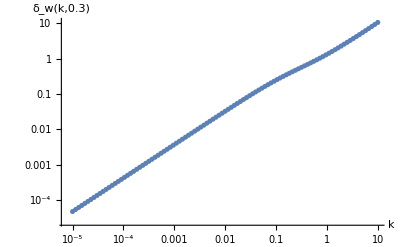

```mathematica
spectrum=getSpectrum[λ,w,imax,kmin,kmax];
```

```mathematica
Subscript[n, T]=getSlopeM[spectrum,imax,1/5][[1]]
```

0.729592

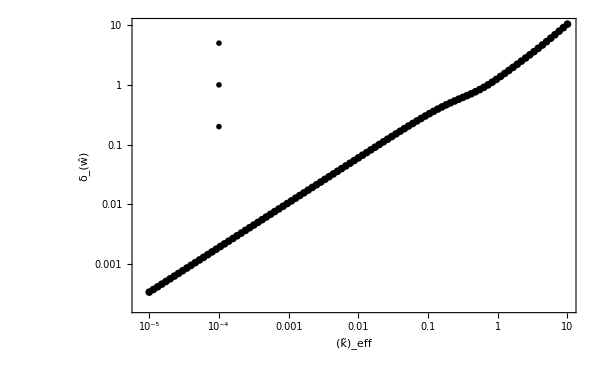

```mathematica
Show[
ListLogLogPlot[spectrum,BaseStyle->texStyle,ImageSize->600,PlotStyle->Black,Frame->True,FrameLabel->{"(k̃)_eff","δ_(ŵ)"}],
Graphics[Style[Text[MaTeX[StringJoin["w=", ToString[NumberForm[w,{2,2}]]],Magnification->3],{Log[10 kmin],Log[5]}],Black]],
Graphics[Style[Text[MaTeX[StringJoin["\\sigma=", ToString[NumberForm[λ,{2,2}]]],Magnification->3],{Log[10 kmin],Log[1]}],Black]],
Graphics[Style[Text[MaTeX[StringJoin["n_T=", ToString[NumberForm[Subscript[n, T],{2,2}]]],Magnification->3],{Log[10 kmin],Log[0.2]}],Black]]
]
```

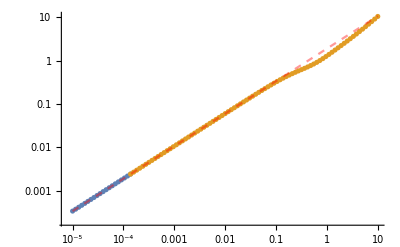

Slope: 0.749407

```mathematica
getSlope[spectrum,imax,1/5];
```

The mode k: 1/(1000 10^(4/5)) or: 0.000158489

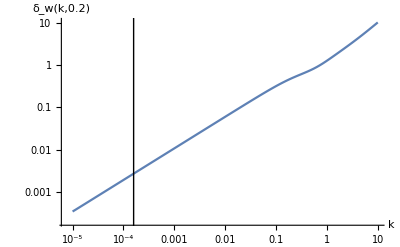

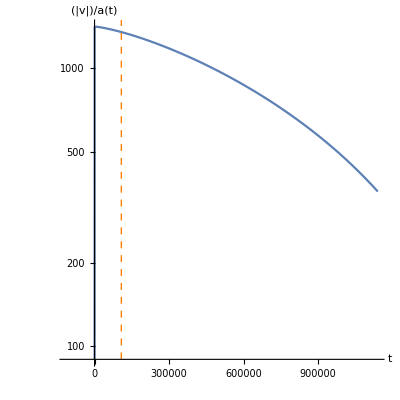

```mathematica
showModeEvolution[20,imax,kmin,kmax,λ,w,spectrum]
```

### Comparison between spectra with and without c_g^2(t)

Step: 0 of: 100

Step: 10 of: 100

Step: 20 of: 100

Step: 30 of: 100

Step: 40 of: 100

Step: 50 of: 100

Step: 60 of: 100

Step: 70 of: 100

Step: 80 of: 100

Step: 90 of: 100

Step: 100 of: 100

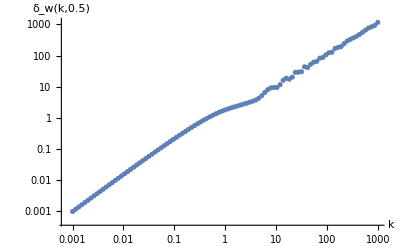

Step: 0 of: 100

Step: 10 of: 100

Step: 20 of: 100

Step: 30 of: 100

Step: 40 of: 100

Step: 50 of: 100

Step: 60 of: 100

Step: 70 of: 100

Step: 80 of: 100

Step: 90 of: 100

Step: 100 of: 100

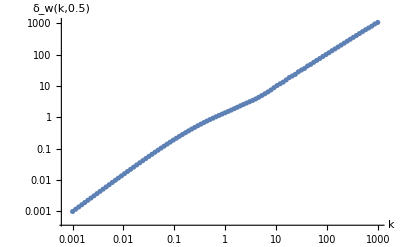

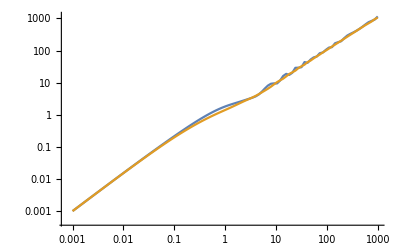

```mathematica
spectrum=getSpectrum[λ,w,imax,kmin,kmax];
spectrumFixed=getSpectrumOLD[λ,w,imax,kmin,kmax];
ListLogLogPlot[{spectrum,spectrumFixed},Joined->True]
```

## λ dependence

```mathematica
λ=0.5;
w=0.5;
imax=100;
kmin=1*10^-4;
kmax=1*10^3;
Print["Amplification: ",(1+λ^2)^(-1/(3w+1))];
Print["Tensor spectral index: ", (6w)/(3w+1)]
```

Amplification: 0.91461

Tensor spectral index: 1.2

```mathematica
(*Orange plot shows the potential in the limit λ->0*)
Manipulate[Plot[{POT[t,l,v],V[t,v]},{t,-2,2},PlotRange->All,AxesLabel->{"t","V(t)"}],{{l,λ,"λ"},0.001,1},{{v,w,"w"},-1,0.99}]
```

Step: 0 of: 100

Step: 10 of: 100

Step: 20 of: 100

Step: 30 of: 100

Step: 40 of: 100

Step: 50 of: 100

Step: 60 of: 100

Step: 70 of: 100

Step: 80 of: 100

Step: 90 of: 100

Step: 100 of: 100

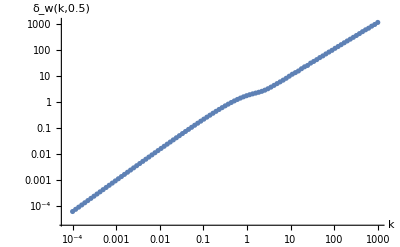

Step: 0 of: 100

Step: 10 of: 100

Step: 20 of: 100

Step: 30 of: 100

Step: 40 of: 100

Step: 50 of: 100

Step: 60 of: 100

Step: 70 of: 100

Step: 80 of: 100

Step: 90 of: 100

Step: 100 of: 100

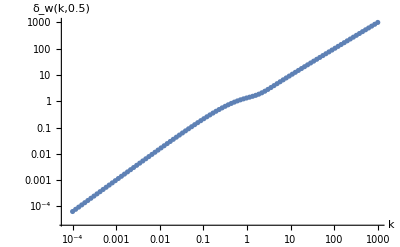

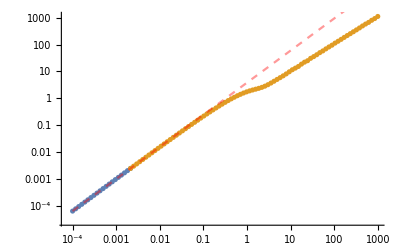

Slope: 1.19572

1.19572

```mathematica
spectrum1=getSpectrum[λ,w,imax,kmin,kmax];
spectrum2=getSpectrum[0.01,w,imax,kmin,kmax];
getSlope[spectrum1,imax,1/5]
```

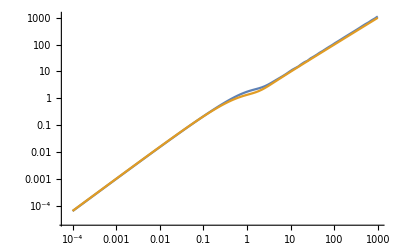

```mathematica
ListLogLogPlot[{spectrum1,spectrum2},Joined->True]
```

```mathematica
spectrum2[[3,2]]/spectrum1[[3,2]]
```

1.01398

Step: 0 of: 100

Step: 10 of: 100

Step: 20 of: 100

Step: 30 of: 100

Step: 40 of: 100

Step: 50 of: 100

Step: 60 of: 100

Step: 70 of: 100

Step: 80 of: 100

Step: 90 of: 100

Step: 100 of: 100

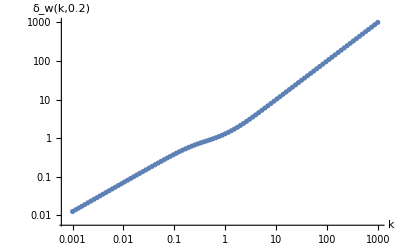

Step: 0 of: 100

Step: 10 of: 100

Step: 20 of: 100

Step: 30 of: 100

Step: 40 of: 100

Step: 50 of: 100

Step: 60 of: 100

Step: 70 of: 100

Step: 80 of: 100

Step: 90 of: 100

Step: 100 of: 100

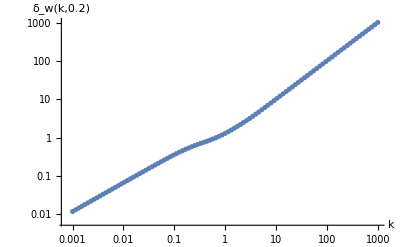

Step: 0 of: 100

Step: 10 of: 100

Step: 20 of: 100

Step: 30 of: 100

Step: 40 of: 100

Step: 50 of: 100

Step: 60 of: 100

Step: 70 of: 100

Step: 80 of: 100

Step: 90 of: 100

Step: 100 of: 100

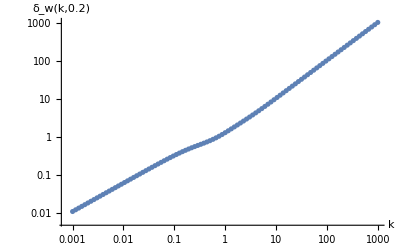

Step: 0 of: 100

Step: 10 of: 100

Step: 20 of: 100

Step: 30 of: 100

Step: 40 of: 100

Step: 50 of: 100

Step: 60 of: 100

Step: 70 of: 100

Step: 80 of: 100

Step: 90 of: 100

Step: 100 of: 100

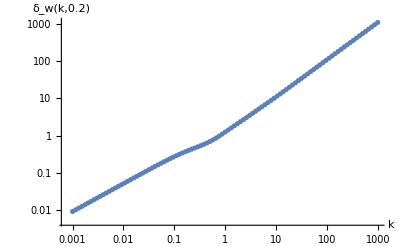

Step: 0 of: 100

Step: 10 of: 100

Step: 20 of: 100

Step: 30 of: 100

Step: 40 of: 100

Step: 50 of: 100

Step: 60 of: 100

Step: 70 of: 100

Step: 80 of: 100

Step: 90 of: 100

Step: 100 of: 100

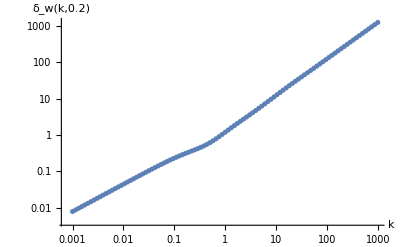

```mathematica
spectrum1=getSpectrum[0.1,w,imax,kmin,kmax];
spectrum2=getSpectrum[0.3,w,imax,kmin,kmax];
spectrum3=getSpectrum[0.5,w,imax,kmin,kmax];
spectrum4=getSpectrum[0.7,w,imax,kmin,kmax];
spectrum5=getSpectrum[0.9,w,imax,kmin,kmax];
```

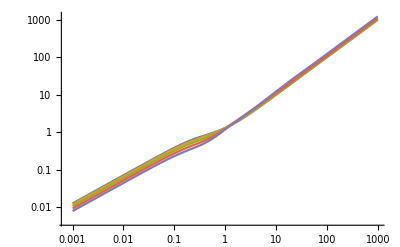

```mathematica
ListLogLogPlot[{spectrum1,spectrum2,spectrum3,spectrum4,spectrum5},Joined->True]
```

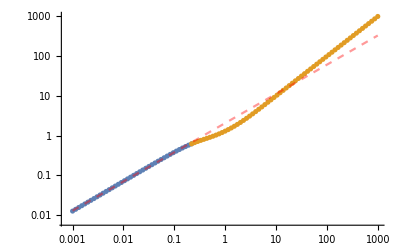

Slope: 0.734805

0.734805

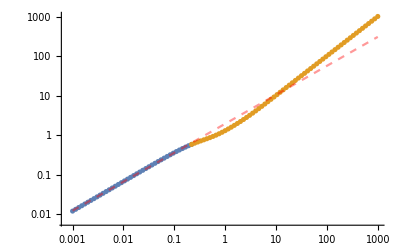

Slope: 0.733636

0.733636

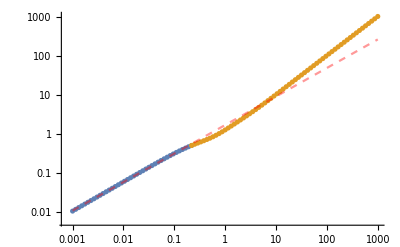

Slope: 0.731318

0.731318

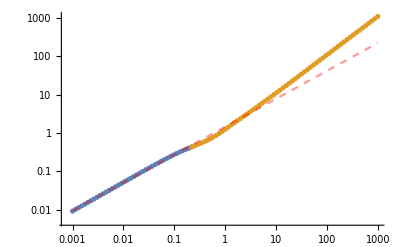

Slope: 0.727931

0.727931

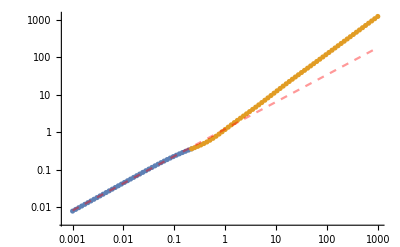

Slope: 0.723656

0.723656

```mathematica
getSlope[spectrum1,imax,2/5]
getSlope[spectrum2,imax,2/5]
getSlope[spectrum3,imax,2/5]
getSlope[spectrum4,imax,2/5]
getSlope[spectrum5,imax,2/5]
```

```mathematica
kmin=10^-3;
kmax=10^2;
```

Step: 0 of: 100

Step: 10 of: 100

Step: 20 of: 100

Step: 30 of: 100

Step: 40 of: 100

Step: 50 of: 100

Step: 60 of: 100

Step: 70 of: 100

Step: 80 of: 100

Step: 90 of: 100

Step: 100 of: 100

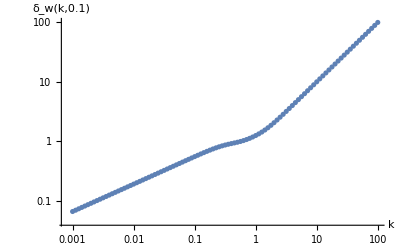

Step: 0 of: 100

Step: 10 of: 100

Step: 20 of: 100

Step: 30 of: 100

Step: 40 of: 100

Step: 50 of: 100

Step: 60 of: 100

Step: 70 of: 100

Step: 80 of: 100

Step: 90 of: 100

Step: 100 of: 100

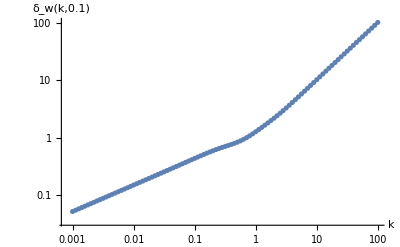

```mathematica
spectrum1=getSpectrum[0.01,0.1,imax,kmin,kmax];
spectrum2=getSpectrum[0.5,0.1,imax,kmin,kmax];
```

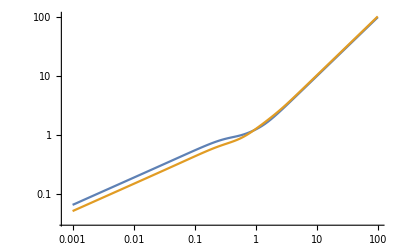

```mathematica
ListLogLogPlot[{spectrum1,spectrum2},Joined->True]
```

```mathematica
spectrum2[[1,2]]/spectrum1[[1,2]]
```

0.784008

```mathematica
(((1+0.5^2)^((3*v)/(3*v+1)))/((1+0.01^2)^((3*v)/(3*v+1))))/.v->0.2
```

1.08724

```mathematica
(1+0.5^2)^((3*0.2)/(3*0.2+1))
```

1.08728

```mathematica
amp={{0.1,0.7840084109051089},{0.2,0.8353434414179486},{0.3, 0.8813767500134267},{0.4,0.9093051910160526},{0.5,0.9867848131952887},{0.6,1.0100099940714158},{0.7,1.1450406161366327}}
```

{{0.1,0.784008},{0.2,0.835343},{0.3,0.881377},{0.4,0.909305},{0.5,0.986785},{0.6,1.01001},{0.7,1.14504}}

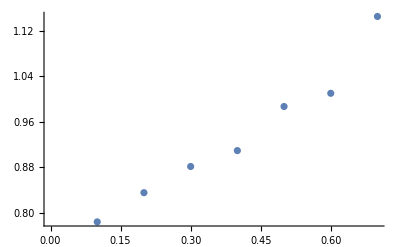

```mathematica
ListPlot[amp]
```

```mathematica
1+0.5^2
```

1.25

## Plots

```mathematica
λ=0.5;
w=0.2;
imax=100;
kmin=2*10^-5;
kmax=1*10^1;
Print["Slope: ", nT[w]];
```

Slope: 0.75

Step: 0 of: 100

Step: 10 of: 100

Step: 20 of: 100

Step: 30 of: 100

Step: 40 of: 100

Step: 50 of: 100

Step: 60 of: 100

Step: 70 of: 100

Step: 80 of: 100

Step: 90 of: 100

Step: 100 of: 100

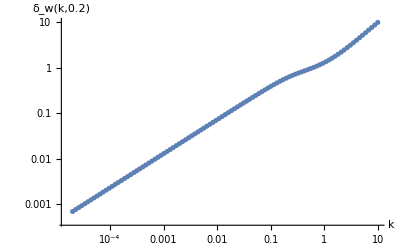

```mathematica
spectrum1=getSpectrumSem[w,imax,kmin,kmax];
```

Step: 0 of: 100

Step: 10 of: 100

Step: 20 of: 100

Step: 30 of: 100

Step: 40 of: 100

Step: 50 of: 100

Step: 60 of: 100

Step: 70 of: 100

Step: 80 of: 100

Step: 90 of: 100

Step: 100 of: 100

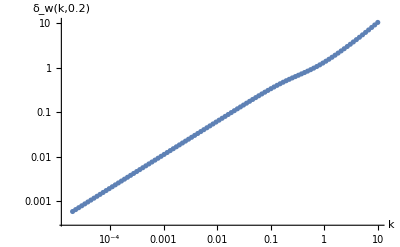

```mathematica
spectrum2=getSpectrum[λ,w,imax,kmin,kmax];
```

```mathematica
Show[
ListLogLogPlot[spectrum,BaseStyle->texStyle,ImageSize->600,PlotStyle->Black,Frame->True,FrameLabel->{"(k̃)_eff","δ_(ŵ)"}],
Graphics[Style[Text[MaTeX[StringJoin["w=", ToString[NumberForm[w,{2,2}]]],Magnification->3],{Log[10 kmin],Log[5]}],Black]],
Graphics[Style[Text[MaTeX[StringJoin["\\sigma=", ToString[NumberForm[λ,{2,2}]]],Magnification->3],{Log[10 kmin],Log[1]}],Black]],
Graphics[Style[Text[MaTeX[StringJoin["n_t=", ToString[NumberForm[Subscript[n, T],{2,2}]]],Magnification->3],{Log[10 kmin],Log[0.2]}],Black]],
Plot[f/.x->y,{y,Log[0.1kmin],Log[10kmax]},PlotStyle->{Gray,Dashed}]
]
```

ListLogLogPlot::lpn: spectrum is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLogLogPlot::lpn will be suppressed during this calculation.

$Aborted

### Semiclassical plots

#### Spectra Comparison

```mathematica
imax=100;
kmin=2*10^-7;
kmax=1*10^0;
```

Step: 0 of: 100

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Step: 10 of: 100

Step: 20 of: 100

Step: 30 of: 100

Step: 40 of: 100

Step: 50 of: 100

Step: 60 of: 100

Step: 70 of: 100

Step: 80 of: 100

Step: 90 of: 100

Step: 100 of: 100

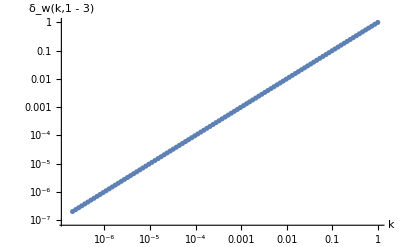

Step: 0 of: 100

Step: 10 of: 100

Step: 20 of: 100

Step: 30 of: 100

Step: 40 of: 100

Step: 50 of: 100

Step: 60 of: 100

Step: 70 of: 100

Step: 80 of: 100

Step: 90 of: 100

Step: 100 of: 100

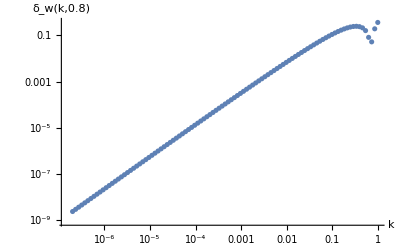

Step: 0 of: 100

Step: 10 of: 100

Step: 20 of: 100

Step: 30 of: 100

Step: 40 of: 100

Step: 50 of: 100

Step: 60 of: 100

Step: 70 of: 100

Step: 80 of: 100

Step: 90 of: 100

Step: 100 of: 100

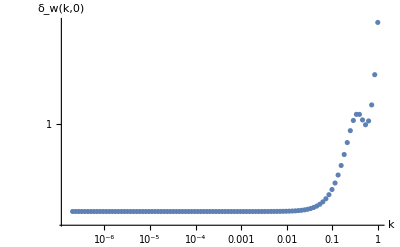

Step: 0 of: 100

Step: 10 of: 100

Step: 20 of: 100

Step: 30 of: 100

Step: 40 of: 100

Step: 50 of: 100

Step: 60 of: 100

Step: 70 of: 100

Step: 80 of: 100

Step: 90 of: 100

Step: 100 of: 100

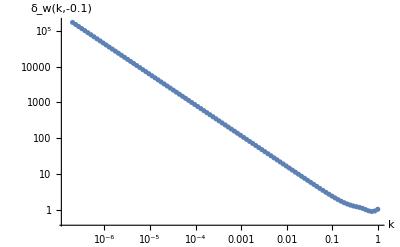

```mathematica
spectrum1=getSpectrumSem[1/3,imax,kmin,kmax];
spectrum2=getSpectrumSem[0.8,imax,kmin,kmax];
spectrum3=getSpectrumSem[0,imax,kmin,kmax];
spectrum4=getSpectrumSem[-0.1,imax,kmin,kmax];
```

```mathematica
f1=getSlopeM[spectrum1,imax,1/5][[2]]
f2=getSlopeM[spectrum2,imax,1/5][[2]]
f3=getSlopeM[spectrum3,imax,1/5][[2]]
f4=getSlopeM[spectrum4,imax,1/5][[2]]
```

0.+1. x

1.7282+1.40283 x

-0.101922-2.72954×10^-6 x

-1.16121-0.857148 x

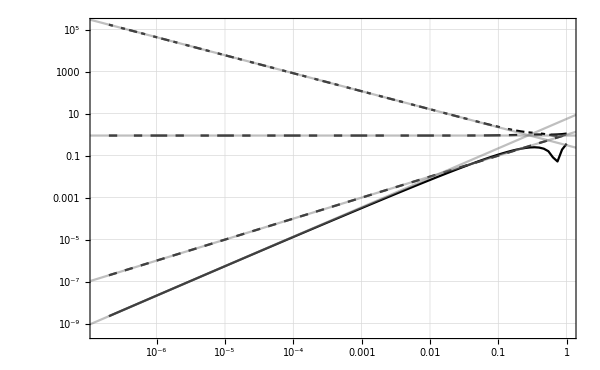

```mathematica
spectrumComparison=Show[
ListLogLogPlot[{spectrum2,spectrum1,spectrum3,spectrum4},Joined->True,PlotTheme->"Detailed",BaseStyle->texStyle,ImageSize->600,FrameLabel->{MaTeX["\\tilde{k}",Magnification->2],MaTeX["\\delta_{\\hat{h}}",Magnification->2]},RotateLabel->False,PlotStyle->{{Black},{Black,Dashing[0.01]},{Black,Dashing[{0.01,0.02,0.01}]},{Black,Dashing[{0.005,0.01,0.005}]}},PlotLegends->{MaTeX[StringJoin["w=0.8\\ n_t=",ToString[NumberForm[(f2-(f2/.x->0))/.x->1,{2,1}]]],Magnification->2],MaTeX[StringJoin["w=1/3\\ n_t=",ToString[NumberForm[(f1-(f1/.x->0))/.x->1,{2,1}]]],Magnification->2],MaTeX[StringJoin["w=0.0\\ n_t=0.0"],Magnification->2],MaTeX[StringJoin["w=-0.1\\ n_t=",ToString[NumberForm[(f4-(f4/.x->0))/.x->1,{2,1}]]],Magnification->2]},FrameTicksStyle->Black],Plot[f1,{x,Log[0.5kmin],Log[5*kmax]},PlotStyle->{Gray,Opacity[0.5]}],
Plot[f2,{x,Log[0.5kmin],Log[5*kmax]},PlotStyle->{Gray,Opacity[0.5]}],
Plot[f3,{x,Log[0.5kmin],Log[5*kmax]},PlotStyle->{Gray,Opacity[0.5]}],
Plot[f4,{x,Log[0.5kmin],Log[5*kmax]},PlotStyle->{Gray,Opacity[0.5]}]
]
```

```mathematica
spectrumComparison=Show[
ListLogLogPlot[{spectrum2,spectrum1,spectrum3,spectrum4},Joined->True,PlotTheme->"Detailed",BaseStyle->texStyle,ImageSize->600,FrameLabel->{MaTeX["\\tilde{k}",Magnification->2],MaTeX["\\delta_{\\hat{h}}",Magnification->2]},RotateLabel->False,PlotStyle->{{Black},{Black,Dashing[0.01]},{Black,Dashing[{0.01,0.02,0.01}]},{Black,Dashing[{0.005,0.01,0.005}]}},PlotLegends->None,FrameTicksStyle->Black],Plot[f1,{x,Log[0.5kmin],Log[5*kmax]},PlotStyle->{Gray,Opacity[0.5]}],
Plot[f2,{x,Log[0.5kmin],Log[5*kmax]},PlotStyle->{Gray,Opacity[0.5]}],
Plot[f3,{x,Log[0.5kmin],Log[5*kmax]},PlotStyle->{Gray,Opacity[0.5]}],
Plot[f4,{x,Log[0.5kmin],Log[5*kmax]},PlotStyle->{Gray,Opacity[0.5]}],
Graphics[Text[Rotate[MaTeX["w=0.8\\ n_t=1.4",Magnification->2],1.2Pi/10],{Log[10^-5],Log[10^-7]}]],
Graphics[Text[Rotate[MaTeX["w=1/3\\ n_t=1.0",Magnification->2],0.8Pi/10],{Log[10^-5],Log[5*10^-5]}]],
Graphics[Text[Rotate[MaTeX["w=0.0\\ n_t=0.0",Magnification->2],0],{Log[10^-5],Log[5*10^0]}]],
Graphics[Text[Rotate[MaTeX["w=-0.1\\ n_t=-0.9",Magnification->2],-0.7Pi/10],{Log[2*10^-5],Log[2*10^4]}]]
]
```

-Graphics-

```mathematica
Export["Sem_comparison.pdf",spectrumComparison,Background->None]
```

Sem_comparison.pdf

#### Mode evolution

```mathematica
kmin=10^-5;
imax=100;
kmax=1;
```

Step: 0 of: 100

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Step: 10 of: 100

Step: 20 of: 100

Step: 30 of: 100

Step: 40 of: 100

Step: 50 of: 100

Step: 60 of: 100

Step: 70 of: 100

Step: 80 of: 100

Step: 90 of: 100

Step: 100 of: 100

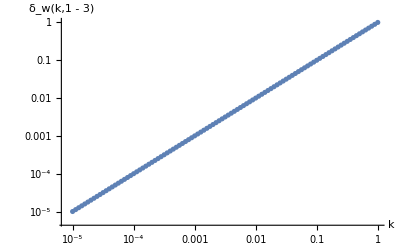

```mathematica
spectrum=getSpectrumSem[1/3,imax,kmin,kmax];
```

```mathematica
showModeEvolutionSem[ti_,timax_,tkmin_,tkmax_,tw_,tspectrum_]:=(
Print["The mode k: ",samplingMode[ti,timax,tkmin,tkmax], " or: ", samplingMode[ti,timax,tkmin,tkmax]//N];
spplt=Show[
ListLogLogPlot[tspectrum,AxesLabel->{"k",StringJoin["δ_w(k,",ToString[tw],")"]},Joined->True],
Graphics[Line[{{Log[samplingMode[ti,timax,tkmin,tkmax]],Log[10^-8]},{Log[samplingMode[ti,timax,tkmin,tkmax]],Log[10^3]}}]]
];
Print[spplt];
tk = samplingMode[ti,timax,tkmin,tkmax];
tmax=(9/2(tw-1)^2/Abs[1-3tw](*cg2*)tk^2)^((3(tw-1))/(2(3tw+1)));
esol=NDSolve[{Qm2Sem[t]^((6tw-2)/(3-3tw))(v''[t]+1/2(6tw-2)/(3-3tw)1/Qm2Sem[t](-(8 t)/(4+8 t^2+4 t^4))v'[t])+(tk^2-POTSem[t,tw])v[t]==0,v[-6tmax]==1/Sqrt[(*Sqrt[cg2[-6 tmax,λ,w]]*) tk],Qm2Sem[-6tmax]^((3tw-1)/(3(1-tw)))v'[-6 tmax]==-I Sqrt[ (*Sqrt[cg2[-6 tmax,λ,w]]*) tk]},v,{t,-10tmax,20tmax}][[1]];
norm=1/aSem[0.5tmax,tw] Re[v[0.5tmax]]/.esol;
plt=Show[
Plot[1/norm 1/aSem[t,tw] Re[v[t]]/.esol,{t,Exp[-2 tmax],10tmax},AxesLabel->{MaTeX["\\tilde{t}",Magnification->2],MaTeX["\\langle \\hat{Q}^{-2} \\rangle^{\\frac{1}{3(1-w)}} | v | (\\tilde{t})",Magnification->2]},AspectRatio->1,PlotStyle->{Black},BaseStyle->texStyle,PlotRange->{Automatic,{-0.5,1.2}}],
(*Graphics[Line[{{tmax,Log[10^-4]},{tmax,Log[10^5]}}]],*)
(*Graphics[{Orange,Dashed,Line[{{t/.FindRoot[POT[t,tλ,tw]-tk^2==0,{t,tmax}],Log[10^-4]},{t/.FindRoot[POT[t,tλ,tw]-tk^2==0,{t,tmax}],Log[10^5]}}]}]*)
Graphics[{Black,Dashed,Line[{{tmax,Log[10^-2]},{tmax,Log[10^5]}}]}],
Graphics[{Black,Dashed,Line[{{-tmax,Log[10^-2]},{-tmax,Log[10^5]}}]}]
];
plt2=Show[
LogLinearPlot[1/norm 1/aSem[t,tw] Re[v[t]]/.esol,{t,0.5tmax,10tmax},FrameLabel->{MaTeX["\\tilde{t}",Magnification->2],MaTeX[(*"\\langle \\hat{Q}^{-2} \\rangle^{\\frac{1}{3(1-w)}} \\Re{(\\mu)} (\\tilde{t})"*)"h",Magnification->2]},RotateLabel->False,PlotStyle->{Black},BaseStyle->texStyle,PlotRange->{Automatic,{-0.5,1.2}},Frame->True],
(*Graphics[Line[{{tmax,Log[10^-4]},{tmax,Log[10^5]}}]],*)
(*Graphics[{Orange,Dashed,Line[{{t/.FindRoot[POT[t,tλ,tw]-tk^2==0,{t,tmax}],Log[10^-4]},{t/.FindRoot[POT[t,tλ,tw]-tk^2==0,{t,tmax}],Log[10^5]}}]}]*)
Graphics[{Black,Dashed,Line[{{tmax,Log[10^-2]},{tmax,Log[10^5]}}]}],
Graphics[{Black,Dashed,Line[{{-tmax,Log[10^-2]},{-tmax,Log[10^5]}}]}],ImageSize->600
];
Print[tmax];
Print[plt];
Print[plt2];
Clear[tk,tmax,esol,plt,spplt,norm];
);
```

The mode k: 1/(10000 10^(19/20)) or: 0.0000112202

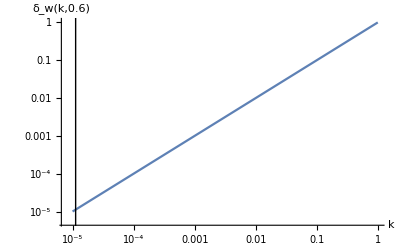

135.28

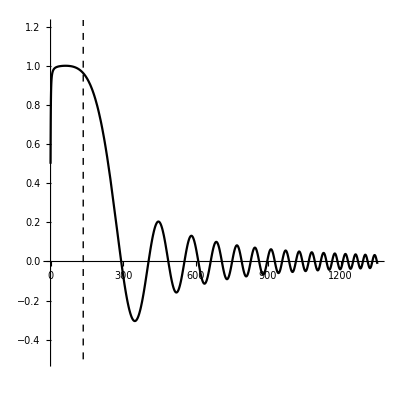

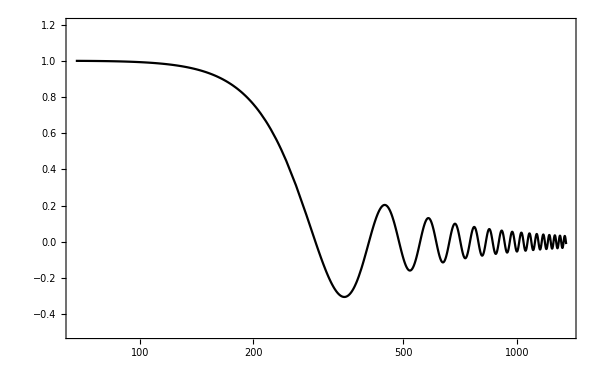

```mathematica
showModeEvolutionSem[1,imax,kmin,kmax,0.6,spectrum]
```

```mathematica
tw=0.5;
Tmax=(9/2(tw-1)^2/Abs[1-3tw](*cg2*)(10^-4)^2)^((3(tw-1))/(2(3tw+1)));
```

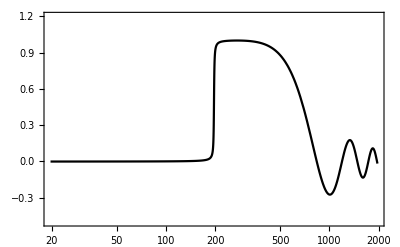

```mathematica
tk=10^-4;
tmax=(9/2(tw-1)^2/Abs[1-3tw](*cg2*)tk^2)^((3(tw-1))/(2(3tw+1)));
esol1=NDSolve[{Qm2Sem[t]^((6tw-2)/(3-3tw))(v''[t]+1/2(6tw-2)/(3-3tw)1/Qm2Sem[t](-(8 t)/(4+8 t^2+4 t^4))v'[t])+(tk^2-POTSem[t,tw])v[t]==0,v[-6tmax]==1/Sqrt[(*Sqrt[cg2[-6 tmax,λ,w]]*) tk],Qm2Sem[-6tmax]^((3tw-1)/(3(1-tw)))v'[-6 tmax]==-I Sqrt[ (*Sqrt[cg2[-6 tmax,λ,w]]*) tk]},v,{t,-10Tmax,20Tmax}][[1]];
norm1=1/aSem[0.5tmax,tw] Re[v[0.5tmax]]/.esol1;
plt1=LogLinearPlot[1/norm1 1/aSem[t-tmax,tw] Re[v[t-tmax]]/.esol1,{t,0.1Tmax,10Tmax},FrameLabel->{MaTeX["\\tilde{t}",Magnification->2],MaTeX[(*"\\langle \\hat{Q}^{-2} \\rangle^{\\frac{1}{3(1-w)}} \\Re{(\\mu)} (\\tilde{t})"*)"h",Magnification->2]},RotateLabel->False,PlotStyle->{Black},BaseStyle->texStyle,PlotRange->{Automatic,{-0.5,1.2}},Frame->True,PlotStyle->Dashed]
```

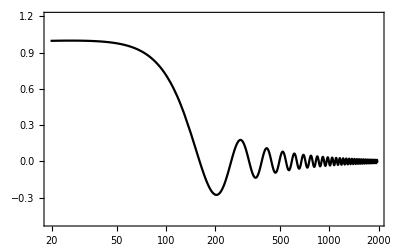

```mathematica
Clear[tk];
tk=10^-3;
tmax=(9/2(tw-1)^2/Abs[1-3tw](*cg2*)tk^2)^((3(tw-1))/(2(3tw+1)));
esol2=NDSolve[{Qm2Sem[t]^((6tw-2)/(3-3tw))(v''[t]+1/2(6tw-2)/(3-3tw)1/Qm2Sem[t](-(8 t)/(4+8 t^2+4 t^4))v'[t])+(tk^2-POTSem[t,tw])v[t]==0,v[-6tmax]==1/Sqrt[(*Sqrt[cg2[-6 tmax,λ,w]]*) tk],Qm2Sem[-6tmax]^((3tw-1)/(3(1-tw)))v'[-6 tmax]==-I Sqrt[ (*Sqrt[cg2[-6 tmax,λ,w]]*) tk]},v,{t,-10Tmax,20Tmax}][[1]];
norm2=1/aSem[0.5tmax,tw] Re[v[0.5tmax]]/.esol2;
plt2=LogLinearPlot[1/norm2 1/aSem[t,tw] Re[v[t]]/.esol2,{t,0.1Tmax,10Tmax},FrameLabel->{MaTeX["\\tilde{t}",Magnification->2],MaTeX[(*"\\langle \\hat{Q}^{-2} \\rangle^{\\frac{1}{3(1-w)}} \\Re{(\\mu)} (\\tilde{t})"*)"h",Magnification->2]},RotateLabel->False,PlotStyle->{Black},BaseStyle->texStyle,PlotRange->{Automatic,{-0.5,1.2}},Frame->True]
```

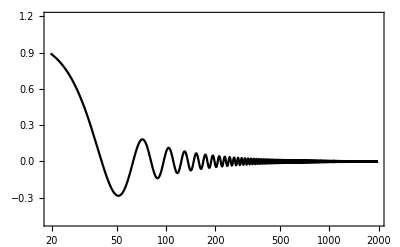

```mathematica
Clear[tk];
tk=10^-2;
tmax=(9/2(tw-1)^2/Abs[1-3tw](*cg2*)tk^2)^((3(tw-1))/(2(3tw+1)));
esol3=NDSolve[{Qm2Sem[t]^((6tw-2)/(3-3tw))(v''[t]+1/2(6tw-2)/(3-3tw)1/Qm2Sem[t](-(8 t)/(4+8 t^2+4 t^4))v'[t])+(tk^2-POTSem[t,tw])v[t]==0,v[-6tmax]==1/Sqrt[(*Sqrt[cg2[-6 tmax,λ,w]]*) tk],Qm2Sem[-6tmax]^((3tw-1)/(3(1-tw)))v'[-6 tmax]==-I Sqrt[ (*Sqrt[cg2[-6 tmax,λ,w]]*) tk]},v,{t,-10Tmax,20Tmax}][[1]];
norm3=-5.6(*1/aSem[0.2tmax,tw] Re[v[0.2tmax]]/.esol3*);
plt2=LogLinearPlot[1/norm3 1/aSem[t,tw] Re[v[t]]/.esol3,{t,0.1Tmax,10Tmax},FrameLabel->{MaTeX["\\tilde{t}",Magnification->2],MaTeX[(*"\\langle \\hat{Q}^{-2} \\rangle^{\\frac{1}{3(1-w)}} \\Re{(\\mu)} (\\tilde{t})"*)"h",Magnification->2]},RotateLabel->False,PlotStyle->{Black},BaseStyle->texStyle,PlotRange->{Automatic,{-0.5,1.2}},Frame->True]
```

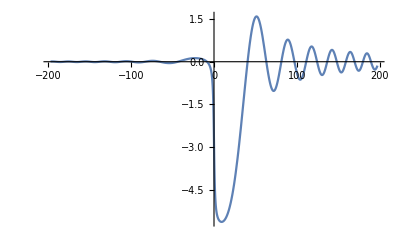

```mathematica
Plot[1/aSem[t,tw] Re[v[t]]/.esol3,{t,-1Tmax,1Tmax},PlotRange->All]
```

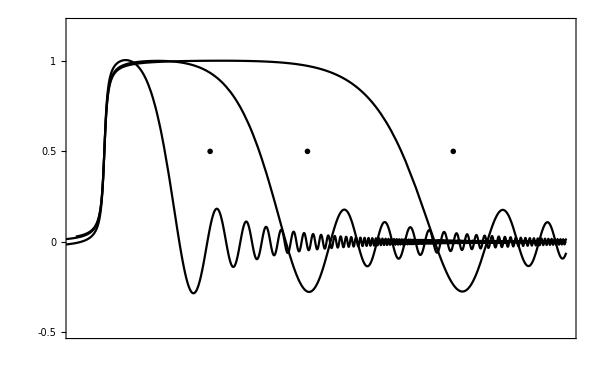

```mathematica
modeEvolution=Show[
LogLinearPlot[1/norm1 1/aSem[t-tmax,tw] Re[v[t-tmax]]/.esol1,{t,0.2Tmax,10Tmax},FrameLabel->{MaTeX["\\tilde{t}",Magnification->2],MaTeX[(*"\\langle \\hat{Q}^{-2} \\rangle^{\\frac{1}{3(1-w)}} \\mathcal{Re}{(\\mu)} (\\tilde{t})"*)"Re(h)",Magnification->2]},RotateLabel->True,PlotStyle->{Black},BaseStyle->texStyle,PlotRange->{Automatic,{-0.5,1.2}},Frame->True,PlotStyle->Dashed,PlotTheme->"Detailed",PlotLegends->None,PlotLabel->MaTeX["w=0.5",Magnification->2],FrameTicksStyle->Black,FrameTicks->{{{-0.5,0,0.5,1},None},{{{tmax,MaTeX["0",Magnification->2]},{2tmax,MaTeX["\\tilde{t}_c",Magnification->2]},{6tmax,MaTeX["5 \\tilde{t}_c",Magnification->2]},{11tmax,MaTeX["10\\tilde{t}_c",Magnification->2]},{31tmax,MaTeX["30\\tilde{t}_c",Magnification->2]}},None}}],
LogLinearPlot[1/norm2 1/aSem[t-tmax,tw] Re[v[t-tmax]]/.esol2,{t,0.01Tmax,10Tmax},FrameLabel->{MaTeX["\\tilde{t}",Magnification->2],MaTeX[(*"\\langle \\hat{Q}^{-2} \\rangle^{\\frac{1}{3(1-w)}} \\Re{(\\mu)} (\\tilde{t})"*)"h",Magnification->2]},RotateLabel->False,PlotStyle->{Black},BaseStyle->texStyle,PlotRange->{Automatic,{-0.5,1.2}},Frame->True],
LogLinearPlot[1/norm3 1/aSem[t-tmax,tw] Re[v[t-tmax]]/.esol3,{t,0.01Tmax,10Tmax},FrameLabel->{MaTeX["\\tilde{t}",Magnification->2],MaTeX[(*"\\langle \\hat{Q}^{-2} \\rangle^{\\frac{1}{3(1-w)}} \\Re{(\\mu)} (\\tilde{t})"*)"h",Magnification->2]},RotateLabel->False,PlotStyle->{Black},BaseStyle->texStyle,PlotRange->{Automatic,{-0.5,1.2}},Frame->True],
Graphics[Text[MaTeX["\\tilde{k}=10^{-2}",Magnification->1.8],{Log[115],0.5}]],
Graphics[Text[MaTeX["\\tilde{k}=10^{-3}",Magnification->1.8],{Log[250],0.5}]],
Graphics[Text[MaTeX["\\tilde{k}=10^{-4}",Magnification->1.8],{Log[800],0.5}]],
ImageSize->600
]
```

```mathematica
Export["modeEvolution.pdf",modeEvolution,Background->None]
```

modeEvolution.pdf

## Exact Evolution

```mathematica
ψ[r_,t_,x0_,p0_,σ_]:=Sqrt[r]σ/(Sqrt[2Pi](I t + σ^2)) Exp[-I p0^2 σ^2 t/(I t + σ^2)]Exp[-p0 x0 t /(I t + σ^2)]Exp[-x0^2/4/(I t + σ^2)]Exp[-r^2/4/(I t + σ^2)]BesselI[1,r(x0+2 I p0 σ^2)/2/(I t + σ^2)]
ψc[r_,t_,x0_,p0_,σ_]:=Sqrt[r]σ/(Sqrt[2Pi](-I t + σ^2)) Exp[I p0^2 σ^2 t/(-I t + σ^2)]Exp[-p0 x0 t /(-I t + σ^2)]Exp[-x0^2/4/(-I t + σ^2)]Exp[-r^2/4/(-I t + σ^2)]BesselI[1,r(x0-2 I p0 σ^2)/2/(-I t + σ^2)]
dψ[r_,t_,x_,p_,s_]:=1/(4 √(2 π) √r (s^2+ⅈ t)^2)ⅇ^(-(r^2+4 ⅈ p^2 s^2 t+4 p t x+x^2)/(4 s^2+4 ⅈ t)) s (r (2 ⅈ p s^2+x) BesselI[0,(r (2 ⅈ p s^2+x))/(2 (s^2+ⅈ t))]+(-2 r^2+2 s^2+2 ⅈ t) BesselI[1,(r (2 ⅈ p s^2+x))/(2 (s^2+ⅈ t))]+r (2 ⅈ p s^2+x) BesselI[2,(r (2 ⅈ p s^2+x))/(2 (s^2+ⅈ t))])
```

```mathematica
x0=30;
σ=2;
p0=-4;
norm=NIntegrate[(ψc[r,0,x0,p0,σ]ψ[r,0,x0,p0,σ]),{r,0,Infinity}]//Chop;
avH =  Chop[NIntegrate[1/norm ψc[r,0,x0,p0,σ](-D[ψ[r,0,x0,p0,σ],{r,2}]+3/4 r^(-2)ψ[r,0,x0,p0,σ]),{r,0,Infinity}],10^(-8)];
avD= Chop[ 1/norm NIntegrate[-I ψc[r,0,x0,p0,σ]r dψ[r,0,x0,p0,σ],{r,0,Infinity}],10^(-6)];
avD =Re[ 1/2(avD + Conjugate[avD])];
tB = -avD/2/avH
```

3.73532

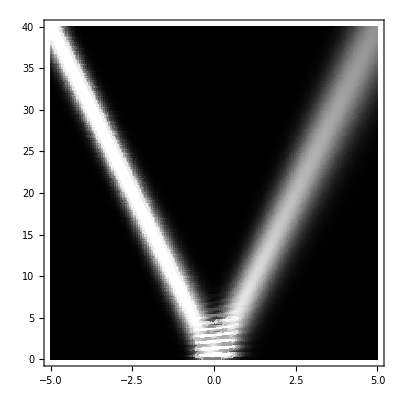

```mathematica
density=DensityPlot[(ψ[x,t+tB,x0,p0,σ]ψc[x,t+tB,x0,p0,σ])/.{p0->-4,x0->30,σ->2},{t,-5,5},{x,0,40},ColorFunction->GrayLevel,MaxRecursion->6,PlotPoints->150,BaseStyle->texStyle,FrameLabel->{MaTeX["\\eta",Magnification->2],MaTeX["q",Magnification->2]},RotateLabel->False,FrameTicksStyle->Black]
```

```mathematica
Export["density.png",density(*,Background->None*)]
```

density.png

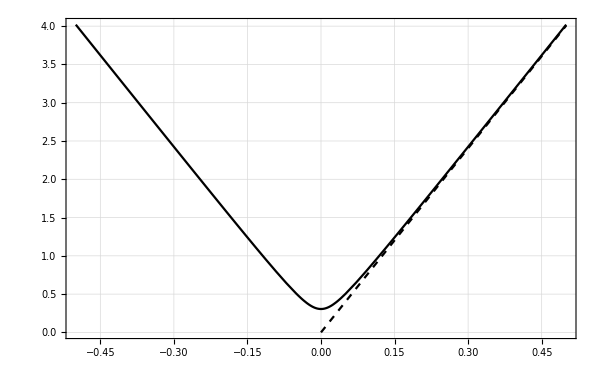

```mathematica
semiTraj=Plot[{Sqrt[(2*3/4)/avH]Sqrt[((Sqrt[2]avH)/Sqrt[3/4] η)^2+1],Sqrt[(2*3/4)/avH]((Sqrt[2]avH)/Sqrt[3/4] η)},{η,-0.5,0.5},PlotStyle->{{Black},{Black,Dashed}},Frame->True,FrameLabel->{MaTeX["\\eta",Magnification->2],MaTeX["q(\\eta)",Magnification->2]},RotateLabel->False,ImageSize->600,PlotTheme->"Detailed",BaseStyle->texStyle,PlotLegends->None,PlotRange->{Automatic,{0,Automatic}}]
```

```mathematica
Export["semi_traj.pdf",semiTraj,Background->None]
```

semi_traj.pdf

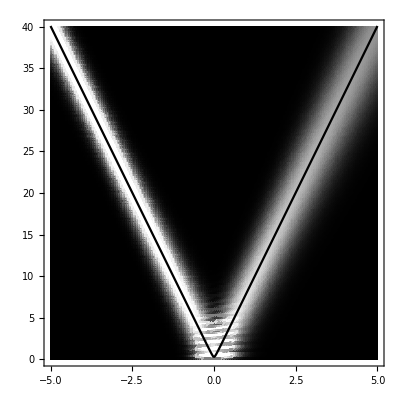

```mathematica
semiDensity=Show[
density=DensityPlot[(ψ[x,t+tB,x0,p0,σ]ψc[x,t+tB,x0,p0,σ])/.{p0->-4,x0->30,σ->2},{t,-5,5},{x,0,40},ColorFunction->GrayLevel,MaxRecursion->6,PlotPoints->150,BaseStyle->texStyle,FrameLabel->{MaTeX["\\eta",Magnification->2],MaTeX["Q",Magnification->2]},RotateLabel->False],
Plot[Sqrt[(2*3/4)/avH]Sqrt[((Sqrt[2]*avH)/Sqrt[3/4] η)^2+1],{η,-5,5},PlotStyle->{Black}]
]
```

```mathematica
Export["semiDensity.png",semiDensity]
```

semiDensity.png

### σ dependence

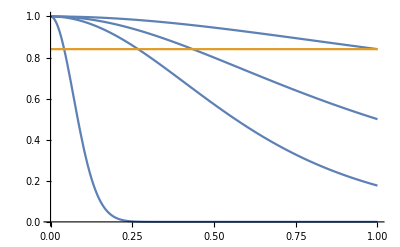

```mathematica
Plot[{(1+σ^2)^(-1/(1+3v))/.v->{-0.33,-0.2,0.0,1},2^(-1/4)},{σ,0,1}]
```

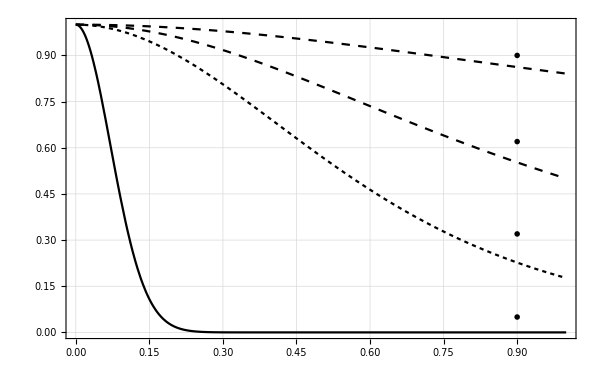

```mathematica
sigma=Show[
Plot[{(1+σ^2)^(-1/(1+3(-0.33))),(1+σ^2)^(-1/(1+3(-0.2))),(1+σ^2)^(-1/(1+3(0.0))),(1+σ^2)^(-1/(1+3(1)))},{σ,0,1},BaseStyle->texStyle,PlotTheme->"Detailed",ImageSize->600,PlotLegends->None,PlotStyle->{{Black},{Black,Dashing[0.005]},{Black,Dashing[0.01]},{Black,Dashing[0.01]},{Gray,Dashed}},FrameLabel->{MaTeX["\\sigma",Magnification->2],MaTeX["(1+\\sigma^2)^{-\\frac{1}{1+3w}}",Magnification->2]},FrameTicksStyle->Black],
Graphics[Text[MaTeX["w=-0.33",Magnification->2],{0.9,0.05}]],
Graphics[Text[MaTeX["w=-0.2",Magnification->2],{0.9,0.32}]],
Graphics[Text[MaTeX["w=0",Magnification->2],{0.9,0.62}]],
Graphics[Text[MaTeX["w=1",Magnification->2],{0.9,0.9}]]
]
```

```mathematica
Export["sigma.pdf",sigma,Background->None]
```

sigma.pdf

```mathematica
2^(-1/(1+1))//N
```

0.707107

### Potentials

```mathematica
Integrate[(Qm2Sem[t]^((3w-1)/(3w-3))),t,Assumptions->{w>0,w<1,λ>0,λ<1}]
```

t (1/(1+t^2))^((1-3 w)/(3-3 w)) (1+t^2)^((1-3 w)/(3-3 w)) Hypergeometric2F1[1/2,(-1+3 w)/(3 (-1+w)),3/2,-t^2]

```mathematica
Manipulate[Plot[t (1/(1+t^2))^((1-3 w)/(3-3 w)) (1+t^2)^((1-3 w)/(3-3 w)) Hypergeometric2F1[1/2,(-1+3 w)/(3 (-1+w)),3/2,-t^2],{t,-10,10}],{w,-1/3,1}]
```

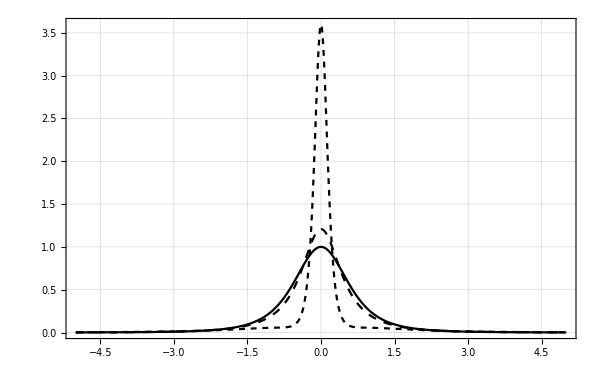

```mathematica
potentials=Plot[{POTSem[t,1/3],POT[t,0.2,1/3],POT[t,0.5,1/3]},{t,-5,5},PlotRange->All,ImageSize->600,Frame->True,PlotTheme->"Detailed",PlotLegends->{MaTeX["\\sigma = 0",Magnification->2],MaTeX["\\sigma = 0.2",Magnification->2],MaTeX["\\sigma = 0.5",Magnification->2]},BaseStyle->texStyle,FrameLabel->{MaTeX["\\eta",Magnification->2],MaTeX["V",Magnification->2]},RotateLabel->False,PlotStyle->{{Black},{Black,Dashing[0.01]},{Black,Dashing[0.007]}},PlotLabel->MaTeX["w=1/3",Magnification->2]]
```

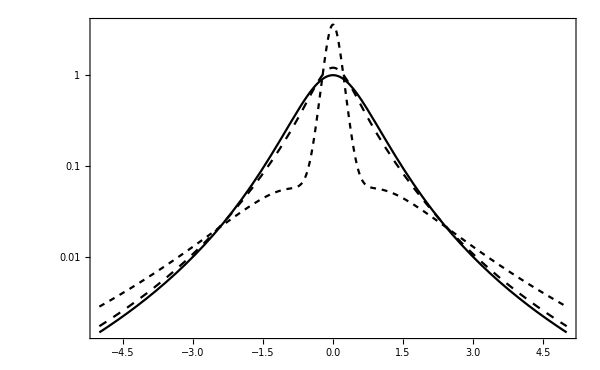

```mathematica
potentialsLog=LogPlot[{POTSem[t,1/3],POT[t,0.2,1/3],POT[t,0.5,1/3]},{t,-5,5},PlotRange->All,ImageSize->600,Frame->True,PlotTheme->"Detailed",PlotLegends->Placed[{MaTeX["\\sigma = 0",Magnification->2],MaTeX["\\sigma = 0.2",Magnification->2],MaTeX["\\sigma = 0.5",Magnification->2]},{Right,Top}],BaseStyle->texStyle,FrameLabel->{MaTeX["\\eta",Magnification->2],MaTeX["V",Magnification->2]},RotateLabel->False,PlotStyle->{{Black},{Black,Dashing[0.01]},{Black,Dashing[0.007]}},PlotLabel->MaTeX["w=1/3",Magnification->2]]
```

```mathematica
Export["potentialsLog.pdf",potentialsLog,Background->None]
```

potentialsLog.pdf

```mathematica
Manipulate[Plot[cg2[t,σ,w],{t,-10,10},PlotRange->{Automatic,{0,1.1}}],{{w,0.333},0.3,0.35},{σ,0.01,0.99}]
```

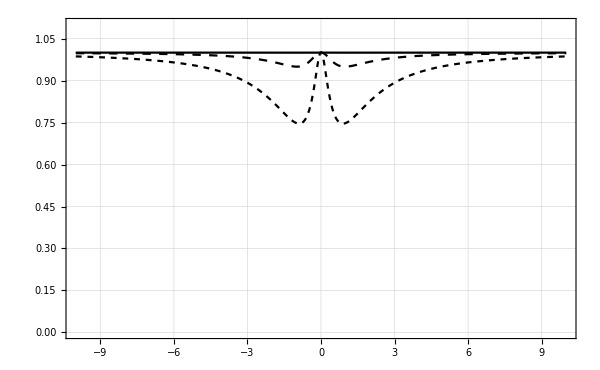

```mathematica
speed=Plot[{cg2[t,0.01,0.33],cg2[t,0.2,0.33],cg2[t,0.5,0.33]},{t,-10,10},PlotRange->{Automatic,{0,1.1}},PlotTheme->"Detailed",PlotStyle->{{Black},{Black,Dashing[0.01]},{Black,Dashing[0.007]}},BaseStyle->texStyle,FrameLabel->{MaTeX["\\eta",Magnification->2],MaTeX["\\frac{c^2_g}{(c^{\\infty}_g)^2}",Magnification->2]},RotateLabel->False,PlotLegends->Placed[{MaTeX["\\sigma = 0",Magnification->2],MaTeX["\\sigma = 0.2",Magnification->2],MaTeX["\\sigma = 0.5",Magnification->2]}
,{Right,Center}],ImageSize->600,PlotLabel->MaTeX["w=1/3",Magnification->2]]
```

```mathematica
Export["speed.pdf",speed,Background->None]
```

speed.pdf

### amplitude comparison

```mathematica
w=0.5;
λ1=0.4;
λ=λ1;
tk=10^-6/Sqrt[cinf[λ,w]];
tmax=(9/2(w-1)^2/Abs[1-3w] cinf[λ,w] tk^2)^((3(w-1))/(2(3w+1)))(1+λ^2)^((3w-1)/(3w+1));
esol1=NDSolve[{Qm2[t,λ]^((6w-2)/(3-3w))(v''[t]+1/2(6w-2)/(3-3w)1/Qm2[t,λ] 1/(8λ)(2t((1-λ)^4-(1+λ)^4))/(((1-λ)^4+t^2)((1+λ)^4+t^2))v'[t])+(cg[t,λ,w] tk^2-POT[t,λ,w])v[t]==0,v[-6tmax]==1/Sqrt[Sqrt[cinf[λ,w]] tk],Qm2[-6tmax,λ]^((3w-1)/(3(1-w)))v'[-6 tmax]==-I Sqrt[ Sqrt[cinf[λ,w]] tk]},v,{t,-6tmax,20tmax}][[1]];
```

```mathematica
w=0.5;
λ1=0.4;
λ=λ1;
tk=10^-6;
tmax=(9/2(w-1)^2/Abs[1-3w] tk^2)^((3(w-1))/(2(3w+1)))(1+λ^2)^((3w-1)/(3w+1));
esol1=NDSolve[{Qm2[t,λ]^((6w-2)/(3-3w))(v''[t]+1/2(6w-2)/(3-3w)1/Qm2[t,λ] 1/(8λ)(2t((1-λ)^4-(1+λ)^4))/(((1-λ)^4+t^2)((1+λ)^4+t^2))v'[t])+(cg2[t,λ,w] tk^2-POT[t,λ,w])v[t]==0,v[-6tmax]==1/Sqrt[Sqrt[cg2[-6tmax,λ,w]] tk],Qm2[-6tmax,λ]^((3w-1)/(3(1-w)))v'[-6 tmax]==-I Sqrt[ Sqrt[cg2[-6tmax,λ,w]] tk]},v,{t,-6tmax,20tmax}][[1]];
```

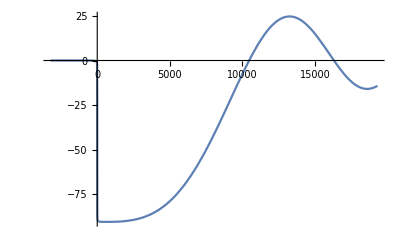

```mathematica
Plot[1/a[t,λ,w] Re[v[t]]/.esol1,{t,-tmax,6tmax}]
```

```mathematica
w=0.5;
tk=10^-6;
tmax=(9/2(w-1)^2/Abs[1-3w](*cg2*)tk^2)^((3(w-1))/(2(3w+1)));
esol2=NDSolve[{Qm2Sem[t]^((6w-2)/(3-3w))(v''[t]+1/2(6w-2)/(3-3w)1/Qm2Sem[t](-(8 t)/(4+8 t^2+4 t^4))v'[t])+(tk^2-POTSem[t,w])v[t]==0,v[-6tmax]==1/Sqrt[(*Sqrt[cg2[-6 tmax,λ,w]]*) tk],Qm2Sem[-6tmax]^((3w-1)/(3(1-w)))v'[-6 tmax]==-I Sqrt[ (*Sqrt[cg2[-6 tmax,λ,w]]*) tk]},v,{t,-6tmax,20tmax}][[1]];
```

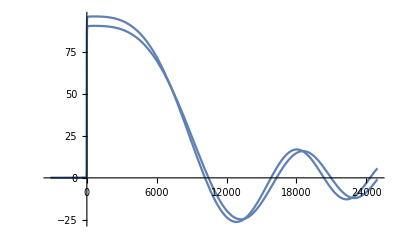

```mathematica
Show[
Plot[-1/a[t,λ1,w]Re[v[t]]/.esol1,{t,-tmax,8tmax},PlotRange->All],
Plot[-1/a[t,λ2,w]Re[v[t]]/.esol2,{t,-tmax,8tmax}]
]
```

95.9596

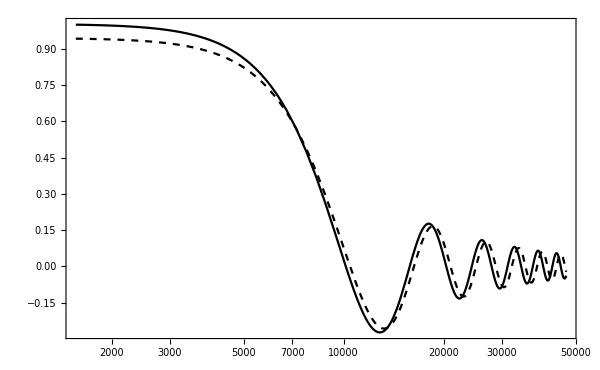

```mathematica
norm=-1/a[0.5tmax,0.001,w]Re[v[0.5tmax]]/.esol2
amplitude=LogLinearPlot[{-1/(norm a[t,λ1,w])Re[v[t]]/.esol1,-1/(norm a[t,λ2,w])Re[v[t]]/.esol2},{t,0.5 tmax,15tmax},PlotRange->All,PlotStyle->{{Black,Dashed},{Black}},BaseStyle->texStyle,ImageSize->600,PlotTheme->"Detailed",PlotLegends->Placed[{MaTeX["\\sigma= 0.4",Magnification->2],MaTeX["\\sigma= 0.0",Magnification->2]},{Right,Top}],PlotLabel->MaTeX["w=0.5,\\ \\tilde{k}_{eff}=10^{-6}",Magnification->2],FrameLabel->{MaTeX["\\tilde{t}",Magnification->2],MaTeX["Re(h)",Magnification->2]},FrameTicksStyle->Black]
```

95.9596

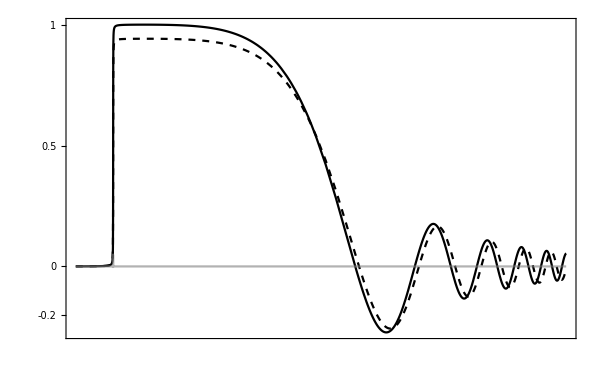

```mathematica
norm=-1/a[0.5tmax,0.001,w]Re[v[0.5tmax]]/.esol2
amplitude=LogLinearPlot[{-1/(norm a[t-tmax,λ1,w])Re[v[t-tmax]]/.esol1,-1/(norm a[t-tmax,λ2,w])Re[v[t-tmax]]/.esol2,POTSem[t-tmax,w]/POTSem[0,w]},{t,0.8 tmax,15tmax},PlotRange->All,FrameTicks->{{{-0.2,0,0.5,1},None},{{{tmax,MaTeX["0",Magnification->2]},{2tmax,MaTeX["\\tilde{t}_c",Magnification->2]},{6tmax,MaTeX["5 \\tilde{t}_c",Magnification->2]},{11tmax,MaTeX["10\\tilde{t}_c",Magnification->2]}},None}},PlotStyle->{{Black,Dashed},{Black},{Gray,Opacity[0.6]}},BaseStyle->texStyle,ImageSize->600,PlotTheme->"Detailed",PlotLegends->Placed[{MaTeX["\\sigma= 0.4",Magnification->2],MaTeX["\\sigma= 0.0",Magnification->2]},{Right,Top}],PlotLabel->MaTeX["w=0.5,\\ \\tilde{k}_{eff}=10^{-6}",Magnification->2],FrameLabel->{MaTeX["\\tilde{t}",Magnification->2],MaTeX["Re(h)",Magnification->2]},FrameTicksStyle->Black]
```

```mathematica
Export["amplitude_comparison.pdf",amplitude,Background->None]
```

amplitude_comparison.pdf

### mode time scaling

```mathematica
w=0.5;
tk=10^-6;
tmax=(9/2(w-1)^2/Abs[1-3w](*cg2*)tk^2)^((3(w-1))/(2(3w+1)));
esol2=NDSolve[{Qm2Sem[t]^((6w-2)/(3-3w))(v''[t]+1/2(6w-2)/(3-3w)1/Qm2Sem[t](-(8 t)/(4+8 t^2+4 t^4))v'[t])+(tk^2-POTSem[t,w])v[t]==0,v[-6tmax]==1/Sqrt[(*Sqrt[cg2[-6 tmax,λ,w]]*) tk],Qm2Sem[-6tmax]^((3w-1)/(3(1-w)))v'[-6 tmax]==-I Sqrt[ (*Sqrt[cg2[-6 tmax,λ,w]]*) tk]},v,{t,-6tmax,20tmax}][[1]];
```

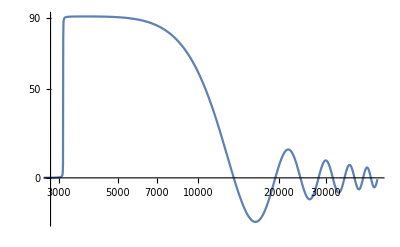

```mathematica
LogLinearPlot[-1/a[t-tmax,λ,w]Re[v[t-tmax]]/.esol1,{t,0,15tmax},PlotRange->{{2800,15tmax},Automatic},Ticks->{{1,{tmax,"0"}},{-30,0,50,90}}]
```

```mathematica
tmax
```

3121.37

## Brudnopis

Step: 0 of: 100

Step: 10 of: 100

Step: 20 of: 100

Step: 30 of: 100

Step: 40 of: 100

Step: 50 of: 100

Step: 60 of: 100

Step: 70 of: 100

Step: 80 of: 100

Step: 90 of: 100

Step: 100 of: 100

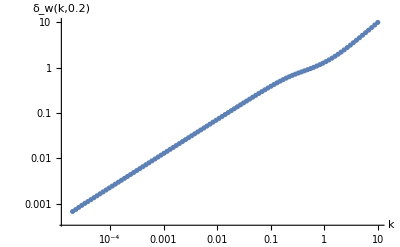

```mathematica
spectrum0=getSpectrum[0.05,w,imax,kmin,kmax];
```

Step: 0 of: 100

Step: 10 of: 100

Step: 20 of: 100

Step: 30 of: 100

Step: 40 of: 100

Step: 50 of: 100

Step: 60 of: 100

Step: 70 of: 100

Step: 80 of: 100

Step: 90 of: 100

Step: 100 of: 100

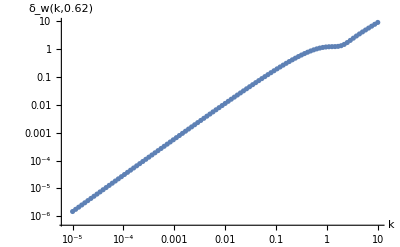

```mathematica
spectrum0=getSpectrum[0.02,w,imax,kmin,kmax];
```

```mathematica
imax=100;
kmin=1*10^-7;
kmax=1*10^0;
```

```mathematica
AA={};
For[nn=0,nn≤50,nn++,
w=0.15+0.5*nn/50+Sqrt[2]/100;
spectrum0=getSpectrumt[0.02,w,imax,kmin,kmax];
spectrum1=getSpectrumt[0.5,w,imax,kmin,kmax];
f0=getSlopeM[spectrum0,imax,1/5][[2]];
f1=getSlopeM[spectrum1,imax,1/5][[2]];
AA=Append[AA,{w,Exp[f0/.x->0]/Exp[f1/.x->0]}];
]
```

```mathematica
AA={};
spectrum0=getSpectrumSem[w,imax,kmin,kmax];
norm=Exp[getSlopeM[spectrum0,imax,1/5][[2]]/.x->0]
For[nn=1,nn≤50,nn++,
w=0.5;
σ=0.1+0.6*nn/50;
spectrum0=getSpectrumt[σ,w,imax,kmin,kmax];
f0=getSlopeM[spectrum0,imax,1/5][[2]];
AA=Append[AA,{σ,Exp[f0/.x->0]/norm}];
]
```

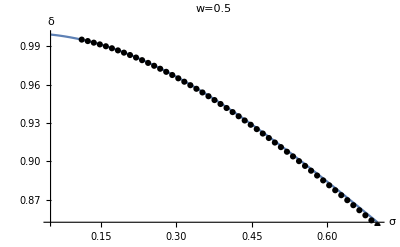

```mathematica
Show[Plot[(1+σ^2)^(-2/5),{σ,0.05,0.7},AxesLabel->{"σ","δ"},PlotLabel->"w=0.5"],ListPlot[AA,PlotStyle->Black]]
```

```mathematica
cg[η_,λ_,w_]:=(3 2^((2 (1+w))/(-1+w)) (-1+w) (1-λ^2)^(4/(3-3 w)) Gamma[2/(3-3 w)] ((1+λ)^(8/(3 (-1+w))) Hypergeometric2F1[2/(3 (-1+w)),(1+3 w)/(3 (-1+w)),(1-3 w)/(3-3 w),-η^2/(-1+λ)^4]-(1-λ)^(8/(3 (-1+w))) Hypergeometric2F1[2/(3 (-1+w)),(1+3 w)/(3 (-1+w)),(1-3 w)/(3-3 w),-η^2/(1+λ)^4]) ((λ+λ^3)/Log[(η^2+(1+λ)^4)/(η^2+(-1+λ)^4)])^((1+3 w)/(3 (-1+w))));
cinf[λ_,w_]:=(((1-λ)^((4 w)/(-1+w)) (1+λ)^(4/(3 (-1+w)))-(1-λ)^(4/(3 (-1+w))) (1+λ)^((4 w)/(-1+w))) Gamma[(1-3 w)/(3 (-1+w))]);
```

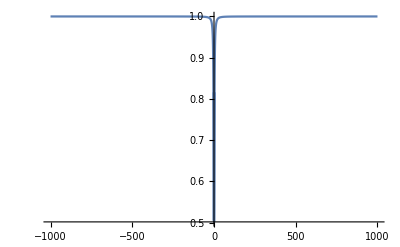

```mathematica
Plot[cg[t,0.5,0.5]/cinf[0.5,0.5],{t,-1000,1000},PlotRange->All]
```

```mathematica
getSpectrumt[λ_,w_,timax_,tkmin_,tkmax_]:=(
tSpectrum={};
For[ti=0,ti≤timax,ti++,
(*If[Mod[ti,10]==0,Print["Step: ",ti, " of: ", timax];,];*)
tk = samplingMode[ti,timax,tkmin,tkmax];
tmax=(9/2(w-1)^2/Abs[1-3w] cinf[λ,w] tk^2)^((3(w-1))/(2(3w+1)))(1+λ^2)^((3w-1)/(3w+1));
esol=NDSolve[{Qm2[t,λ]^((6w-2)/(3-3w))(v''[t]+1/2(6w-2)/(3-3w)1/Qm2[t,λ] 1/(8λ)(2t((1-λ)^4-(1+λ)^4))/(((1-λ)^4+t^2)((1+λ)^4+t^2))v'[t])+(cg[t,λ,w] tk^2-POT[t,λ,w])v[t]==0,v[-6tmax]==1/Sqrt[Sqrt[cinf[λ,w]] tk],Qm2[-6tmax,λ]^((3w-1)/(3(1-w)))v'[-6 tmax]==-I Sqrt[ Sqrt[cinf[λ,w]] tk]},v,{t,-6tmax,tmax}][[1]];
A1=1/a[tmax,λ,w] Abs[v[ tmax]]/.esol;
tSpectrum=Append[tSpectrum,{Sqrt[cinf[λ,w]]tk,(Sqrt[cinf[λ,w]]tk)^(3/2) A1}];
];
Print[Show[ListLogLogPlot[tSpectrum,AxesLabel->{"k",StringJoin["δ_w(k,",ToString[w],")"]}]]];
Clear[ti,tk,tmax,esol];
Return[tSpectrum];
);
```

Skale

```mathematica
Subscript[q, b][K_,w_,zt_,r_]:=√((32π zt^(w-1/3) K)/(23/10 10^120(1.25 10^185)^(w-1/3) r^(w+1)));
Subscript[k, max][K_,w_,zt_,r_]:=(23/10 10^120 r^(w+1)(1.25 10^185)^(w-1/3)zt^(-w+1/3))/(√K);
ℽ[w_]:=(4 √6)/(3(1-w));
Subscript[a, 0]=5 10^61 r^(1/3);
Subscript[k, pivot][r_]:=20 π  r^(1/3);
a[q_,w_]:=(q/ℽ[w])^(2/(3-3w));
Subscript[z, b][K_,w_,zt_,r_]:=Subscript[a, 0]/a[Subscript[q, b][K,w,zt,r],w];
Subscript[k, bounce][K_,w_,zt_,r_]:= Subscript[k, max][K,w,zt,r]((Subscript[q, b][K,w,zt,r])/ℽ[w])^((6w-2)/(3w-3));
kr[K_,w_,zt_,r_]:=(Subscript[k, pivot][r])/(Subscript[k, bounce][K,w,zt,r]);
c2=4π ⅇ^(-ⅈ π/2((3(1-w))/(2(3w+1))+1/2));CC[w_]=c2 √((2Abs[1-3w])/(3w+1)) HankelH2[(3(1-w))/(2(3w+1)), (2Abs[1-3w])/(3w+1)];DD[w_]=c2/(2 √((2Abs[1-3w])/(3w+1)))  HankelH2[(3(1-w))/(2(3w+1)), (2Abs[1-3w])/(3w+1)]+c2/2 √((2Abs[1-3w])/(3w+1))(HankelH2[(3(1-w))/(2(3w+1))-1, (2Abs[1-3w])/(3w+1)]-HankelH2[(3(1-w))/(2(3w+1))+1, (2Abs[1-3w])/(3w+1)]);A[K_,w_,zt_,r_,λ_,q_]:=Abs[(9(1-w)^2)/(2(1-3w))]^(-1/(1+3w))Abs[(2CC[w])/(√(2Abs[1-3w]))-DD[w]] a[q,w]^(3w)((1+λ^2)^((3w)/(1+3w))Subscript[k, max][K,w,zt,r])/2 kr[K,w,zt,r]^((6w)/(3w+1));
```

```mathematica
zt=10^28;
r=2;
ASem[K_,w_,zt_,r_,q_]:=Abs[2CC[w](2Abs[1-3w])^(3/2(1-w)/(1+3w))(9(1-w)^2)^(-1/(3w+1))-((2Abs[1-3w])/(9(1-w)^2))^(1/(3w+1))DD[w]] a[q,w]^(3w)(Subscript[k, max][K,w,zt,r])/2 kr[K,w,zt,r]^((6w)/(3w+1));
F[w_]:=Solve[Log10[ASem[10^KK,w,zt,r,Subscript[q, b][10^KK,w,zt,r]]]==-5,KK]//Flatten;
```

```mathematica
table1={{0.45,140.8},{0.47,145},{0.5,151.02},{0.55,160.1},{0.6,168.5},{0.65,176.4},{0.7,184.1},{0.75,191.5},{0.8,198.8}};
```

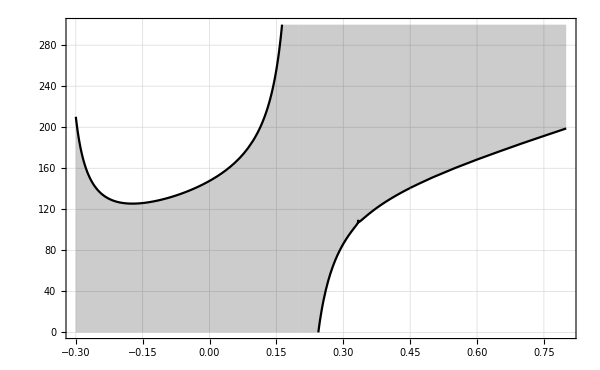

```mathematica
Kw=Show[Plot[KK/.F[w],{w,-0.3,0.2},Exclusions->{0.2},PlotStyle->Black,PlotRange->{{-0.3,0.8},{0,300}},BaseStyle->texStyle,Filling->Bottom,PlotTheme->"Detailed",PlotLegends->None,FrameLabel->{MaTeX["w",Magnification->2],MaTeX["\\log_{10}K",Magnification->2]},ImageSize->600,FrameTicksStyle->Black],
Plot[KK/.F[w],{w,0.2,0.45},Exclusions->{0.2},PlotStyle->Black,Filling->Top,PlotRange->{Automatic,{0,300}}],
ListPlot[table1,Joined->True,Filling->Top,PlotRange->{Automatic,{0,300}},PlotStyle->Black]
]
```

```mathematica
Export["K_w_Scale.pdf",Kw,Background->None]
```

K_w_Scale.pdf

```mathematica
table3=Table[{table1[[k,1]],(Log10[Subscript[z, b][1,table1[[k,1]],10^28,r]]-table1[[k,2]]/(3-3table1[[k,1]]))},{k,1,Length[table1]}]
```

General::munfl: (4.79103×10^-98)^3.33333 is too small to represent as a normalized machine number; precision may be lost.

Power::infy: Infinite expression 1/0. encountered.

{{0.45,60.5091},{0.47,59.819},{0.5,58.8686},{0.55,57.7143},{0.6,56.8472},{0.65,56.2216},{0.7,55.6295},{0.75,55.2332},{0.8,∞}}

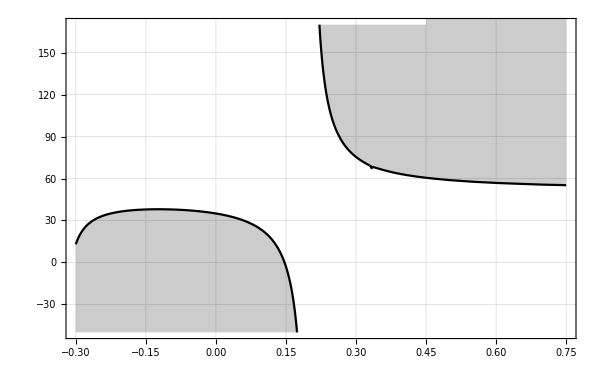

```mathematica
zw=Show[
Plot[(Log10[Subscript[z, b][1,x,10^28,r]]-KK/(3-3x))/.F[x],{x,-0.3,0.2},PlotRange->{{-0.3,0.75},{-50,170}},Exclusions->{0.2},BaseStyle->texStyle,PlotTheme->"Detailed",PlotStyle->Black,PlotLegends->None,FrameLabel->{MaTeX["w",Magnification->2],MaTeX["\\log_{10}z_b",Magnification->2]},ImageSize->600,FrameTicksStyle->Black,Filling->Bottom],
Plot[(Log10[Subscript[z, b][1,x,10^28,r]]-KK/(3-3x))/.F[x],{x,0.2,0.45},Exclusions->{0.2},PlotRange->{{-0.3,0.75},{-50,170}},BaseStyle->texStyle,PlotTheme->"Detailed",PlotStyle->Black,PlotLegends->None,FrameLabel->{MaTeX["w",Magnification->2],MaTeX["\\log_{10}z_b",Magnification->2]},ImageSize->600,Filling->Top],
ListPlot[table3,Joined->True,PlotStyle->Black,Filling->Top,PlotRange->{Automatic,{-100,200}}]
]
```

```mathematica
Export["z_w_Scale.pdf",zw,Background->None]
```

z_w_Scale.pdf

```mathematica
table2=Table[{table1[[k,1]],Limit[Log10[Subscript[ρ, b][10^KK,table1[[k,1]],zt,r]],KK->table1[[k,2]]]},{k,1,Length[table1]}];
```

General::munfl: 9.65501×10^-230 3.10725×10^-115 is too small to represent as a normalized machine number; precision may be lost.

Divide::infy: Infinite expression 1/0. encountered.

General::munfl: 1.17718×10^-271 3.43101×10^-136 is too small to represent as a normalized machine number; precision may be lost.

Divide::infy: Infinite expression 1/0. encountered.

General::munfl: 3.78214×10^-163 3.78214×10^-163 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Divide::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Divide::infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0.^3 encountered.

General::munfl: 1/(10^(1.22289×10^6)) is too small to represent as a normalized machine number; precision may be lost.

Power::infy: Infinite expression 1/0.^1.25001 encountered.

General::munfl: 1/10^1085.43 is too small to represent as a normalized machine number; precision may be lost.

Power::infy: Infinite expression 1/0.^1.25803 encountered.

General::munfl: 1/10^473.637 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Power::infy: Infinite expression 1/0.^1.26616 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

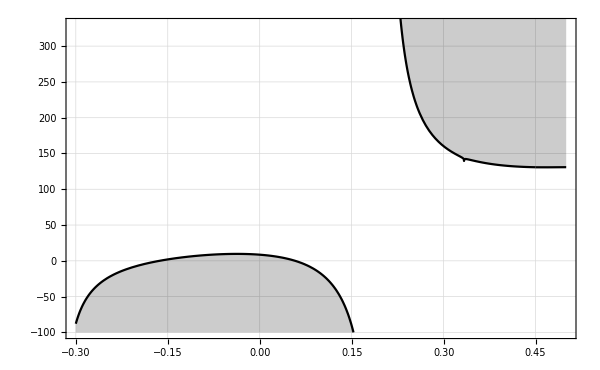

```mathematica
rhow=Show[
Plot[Log10[Subscript[ρ, b][10^KK,x,zt,r]]/.F[x],{x,-0.3,0.2},Exclusions->{0.2},PlotRange->{{-0.3,0.5},{-100,330}},Exclusions->{0.2},BaseStyle->texStyle,PlotTheme->"Detailed",PlotStyle->Black,PlotLegends->None,FrameLabel->{MaTeX["w",Magnification->2],MaTeX["\\log_{10}\\rho_b",Magnification->2]},ImageSize->600,FrameTicksStyle->Black,Filling->Bottom],
Plot[Log10[Subscript[ρ, b][10^KK,x,zt,r]]/.F[x],{x,0.2,0.45},Exclusions->{0.2},AxesLabel->{"w","ρ_b"},PlotStyle->Black,Filling->Top],
ListPlot[table2,Joined->True,PlotStyle->Black,Filling->Top,PlotRange->{Automatic,{0,400}}]
]
```

```mathematica
Export["rho_w_Scale.pdf",rhow,Background->None]
```

rho_w_Scale.pdf